## Generowanie funkcji G(x,y) określającej współczynnik rozpylenia dla punktu (x,y)

Jestem przyzwyczajony do używania znaków ⟦ i ⟧ zamiast [[ i ]], jest to dla mnie czytelniejsze. Wpisuje się je klawiszami escape [[ escape oraz escape ]] escape.

## Wartości stałe

### Rozmiar próbki (200nm x 200nm)

```mathematica
size=500;
```

### Liczba punktów będących zarodkami polikryształów

```mathematica
n=220*size*size/(200*200);
```

```mathematica
(*accuracy=80;*)
```

```mathematica
accuracy=20;
```

```mathematica
precision=3;
```

```mathematica
(*workingPrecision=17;*)
```

```mathematica
workingPrecision=17;
```

```mathematica
minPoints=1;(*IntegerPart[0.99*size]*)
```

```mathematica
(*maxPoints=200;*)
```

```mathematica
maxPoints=101;
```

```mathematica
nomAngleInDegrees=80;
```

```mathematica
(* seedValue=15 daje poprawne wyniki *)
```

```mathematica
seedValue=15;
```

### Minimalna i maksymalna wartość współczynnika rozpylania

```mathematica
minSputter=0.7;
```

```mathematica
maxSputter = 1.2;
```

#### Kąt padania jonów

```mathematica
nomAngle=nomAngleInDegrees*Pi/180
```

(4 π)/9

### Czas trwania

```mathematica
(* doza ion/cm^2*)
```

```mathematica
dosePerCmSq=10^15
```

1000000000000000

```mathematica
(* doza ion/nm^2*)
```

```mathematica
dose=dosePerCmSq/(10^7*10^7)
```

10

```mathematica
(*dose=483;*)
```

```mathematica
dose=800000000
```

800000000

```mathematica
(* 50s *)
```

```mathematica
(*tMax=50000000;*)
```

```mathematica
(*tMax=dose*(size*size/(200*200))*1000000/7.946*)
```

```mathematica
(*tMax=dose*100000*(size*size/(200*200))/7.946*)
```

```mathematica
tMax=dose/7.946
```

1.0068×10^8

```mathematica
(*tMax=500000000;*)
```

## Stworzenie tablicy G

Tu pobawiłem się trochę obsługą plików. Najpierw ustawiam ścieżkę obsługi plików z jakiejś domyślnej na tą gdzie znajduje się ten notebook. Potem jest zwykły if, w którym sprawdzam czy w tym folderze istnieje plik g_raw.dat i zmienna importGQ (czy chcę importować G z pliku) jest równa True. Jeśli tak to go importuję. Jeśli nie to otwieram plik erosion_G_new.nb (nie wiem czemu tutaj nie działa ścieżka ustawiona w SetDirectory dlatego cała konstrukcja z FileNameJoin), wykonuję go w całości i jak się wykona zamykam bez zapisu (dzięki temu outputy w pliku pierwotnym nie zmienią się).

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\lukasz\Dropbox\dissertation\ripple_formation\mathematica

```mathematica
importGQ=True;
```

```mathematica
(*If[
FileExistsQ[StringJoin["data/g_raw_", ToString[size],".dat"]]
&&FileExistsQ[StringJoin["data/seeds_",ToString[size],".dat"]]
&&FileExistsQ[StringJoin["data/sputter_coeffs_",ToString[size], ".dat"]]
&&importGQ,

G=Import[StringJoin["data/g_raw_", ToString[size],".dat"],"Table"];seeds=Import[StringJoin["data/seeds_",ToString[size],".dat"]]; sputterCoeffs=Import[StringJoin["data/sputter_coeffs_",ToString[size], ".dat"]];,

notebookG=NotebookOpen[FileNameJoin[{NotebookDirectory[],"prepare_data.nb"}]];
NotebookEvaluate[notebookG,InsertResults->True];
NotebookClose[notebookG];
]*)
```

```mathematica
If[
FileExistsQ[StringJoin["data/g_raw_500.dat"]]
&&FileExistsQ[StringJoin["data/seeds_500.dat"]]
&&FileExistsQ[StringJoin["data/sputter_coeffs_500.dat"]]
&&importGQ,

G=Import[StringJoin["data/g_raw_500.dat"],"Table"];seeds=Import[StringJoin["data/seeds_500.dat"]]; sputterCoeffs=Import[StringJoin["data/sputter_coeffs_500.dat"]];,

notebookG=NotebookOpen[FileNameJoin[{NotebookDirectory[],"prepare_data.nb"}]];
NotebookEvaluate[notebookG,InsertResults->True];
NotebookClose[notebookG];
]
```

## Dalsze obliczenia

### Przypisanie do poszczególnych krystalitów ich współczynników rozpylania

Używasz (szczególnie w obliczeniach G, które dałem do osobnego pliku) konstrukcji For, które nie są w Mathematice najwydajniejsze. Wszędzie tam gdzie chodzisz po liście można to zrobić funkcją Table, która jest dużo szybsza. Przepisałem twoje konstrukcje tak, żeby używały Table zapisując wyniki w zmiennych z dopisanym “2”. Żeby pokazać ci jakie są różnice w czasie wykonywania obu typów konstrukcji objąłem je funkcją AbsoluteTiming, która zwraca czas wykonywania instrukcji (całkowity, łącznie z czasem jaki jest potrzebny na wyświetlenie wyników, itp.).

```mathematica
G2=G;
```

```mathematica
AbsoluteTiming[
For[i=1,i≤size+1,++i,
For[j=1,j≤size+1,++j,
G[[i,j]]=sputterCoeffs[[G[[i,j]]]][[1]]
(* Random sputter coeffs *)
(*G[[i,j]]=sputterCoeffs[[G[[i,j]]]][[1]]*)
(* Test 1 *)
(* All the same sputter coeff 1.0 *)
(*G[[i,j]]=1.0*)
(* Test 2 *)
(* Two sputter coeffs 0.7 and 1.2 *)
(*G[[i,j]]=If[i≤size/2,0.7,1.2]*)
]
]
]
```

{1.58225,Null}

```mathematica
i=.
j=.
k=.
```

```mathematica
(*AbsoluteTiming[
G2=Table[sputterCoeffs⟦G2⟦i,j⟧⟧,{i,size+1},{j,size+1}];
]*)
```

Zamiast Rotate wpisałem Reverse i Transpose czyli zamiast obracać obrazek (i przy okazji wszystkie osie, legendy, itp.) obróciłem dane.

```mathematica
G;
```

```mathematica
G[[1;;size,1;;size]];
```

```mathematica
ArrayPlot[Reverse[Transpose[G[[1;;size,1;;size]]]], ColorFunction->(ColorData["Rainbow"][1-#]&), PlotLegends->Automatic]
```

-Graphics-

Tutaj było clue problemu. Niestety Part (czyli ⟦ ⟧) nie może być wykonane jeśli indeksy nie są numeryczne. W Mathematice 10 wprowadzono funkcję Indexed, która robi dokładnie to co jest potrzebne czyli wyciąga coś z listy jeśli ma podane indeksy numeryczne a jak indeksy są symboliczne to pozostaje w formie abstrakcyjnej (symbolicznej). Jeśli chciałbyś mieć funkcję, która będzie działała we wcześniejszych wersjach to działać powinno rozwiązanie wykomentowane poniżej.

```mathematica
(*ListPart[x_List,spec__]:=x[[spec]];
Gfun2Old[x_,y_,t_]:=ListPart[G,Floor[x+1],Floor[y+1]]*)
```

```mathematica
(*mając tablicę G tworzę funkcję zwracającą wartość G dla pary(x,y)*)
Gfun[xparam_,yparam_,tparam_]:=G⟦Floor[xparam+1],Floor[yparam+1]⟧
```

```mathematica
Gfun2[xparam_,yparam_,tparam_]:=Indexed[G,{Floor[xparam+1],Floor[yparam+1]}]
```

```mathematica
Indexed[G,{Floor[2],Floor[3]}]
```

1.13474

### Ten sam rysunek (z użyciem tych samych zarodków ziaren, bez kolorowania) z użyciem VoronoiMesh - funkcji wbudowanej w Mathematicę

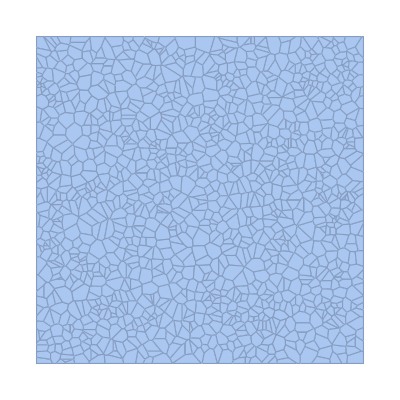

```mathematica
vor = VoronoiMesh[seeds, {{0, size+1}, {0,size+1}}]
```

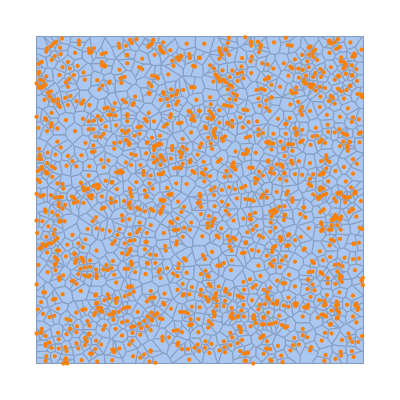

```mathematica
Show[%, Graphics[{Orange, Point[seeds]}]]
```

```mathematica
cells=MeshPrimitives[vor,2];
```

### Funkcja Yammamury

```mathematica
(* bierze pod uwagę zmianę współczynnika rozpylania spowodowaną zmianą lokalnego kąta padania strumienia *)
```

```mathematica
Y0=33/10; (* atom/jon współczynnik rozpylania dla strumienia padającego pod kątem prostym *)
```

```mathematica
f=195/100; (* bezwymiarowy współczynnik opisujący kształt zależności kątowej *)
```

#### Kąt dla którego współczynnik rozpylania jest największy

```mathematica
thOpt=70 * Pi/180
```

(7 π)/18

```mathematica
thOpt=70°
```

70 °

#### Definicja funkcji Yammamury

```mathematica
yammFormula[th_]:=Y0*Cos[th ]^-f*Exp[f*(1-Cos[th ]^-1)*Cos[thOpt]]
```

```mathematica
(* test funkcji Yammamury dla kątów od 0° do 90° *)
```

Wszystkie opisy osi, jeśli nie mają być pod nie podstawione zmienne, lepiej jest, żeby były wpisane jako string czyli otoczone cudzysłowami.

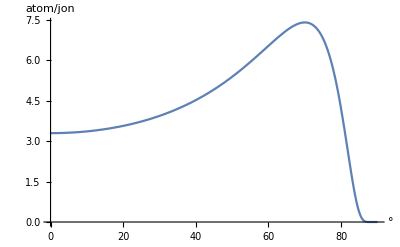

```mathematica
Plot[yammFormula[th Degree], {th,0,90},AxesLabel->{"°","atom/jon"}]
```

### Funkcja odpowiadająca za erozję powierzchni

```mathematica
Clear[h]
```

```mathematica
(* objętość atomu niklu *)
```

```mathematica
omega=1/(917/10);
```

```mathematica
(* strumień jonów *)
```

```mathematica
phi=7946/1000000000; (*jonów /us *)
```

```mathematica
(* funkcja opisująca zależność cosinus lokalnego kąta padania od nominalnego kąta padania *)
```

Jako argument przekazujesz tylko nazwę funkcji, bez jej parametrów. Jeśli musiałbyś przekazać też bezpośrednio argumenty funkcji h to powinieneś je dodać jako zwykłe argumenty. Za to w samej funkcji zrobiłeś właściwie czyli musisz podać bezpośrednio wszystkie argumenty dla funkcji h.

```mathematica
cosThLocFormula[h_,x_,y_,t_,thNom_]:=(Sin[thNom]*D[h[x,y,t],x]+Cos[thNom])/Sqrt[D[h[x,y,t],y]^2+1+D[h[x,y,t],x]^2]
```

```mathematica
(* funkcja opisująca cosinus kąta pomiędzy normalną do lokalnej płaszczyzny a normalną do średniej płaszczyzny *)
```

```mathematica
cosThOffFormula[h_,x_,y_,t_]:=1/Sqrt[D[h[x,y,t],y]^2+1+D[h[x,y,t],x]^2]
```

```mathematica
EFormula[h_,x_,y_,t_,thNom_]:=-omega*phi*cosThLocFormula[h,x,y,t,thNom]/cosThOffFormula[h,x,y,t]*yammFormula[ArcCos[cosThLocFormula[h,x,y,t,thNom]]]*Gfun2[x,y,t]
```

### Funkcja odpowiadająca za dyfuzję powierzchni

```mathematica
(* współczynnik dyfuzji powierzchni *)
```

```mathematica
B=375/100
```

15/4

```mathematica
nCoeff=375/10
```

75/2

```mathematica
noise = Import[StringJoin["data/noise_500.dat"]];
```

```mathematica
noise[[2,3]]
```

1/2

```mathematica
(* równomierny losowny szum z przedziału [-0.5,0.5] *)
```

```mathematica
noiseFun[xp_,yp_,tp_]:=Indexed[noise,{Floor[xp+1],Floor[yp+1]}];
```

```mathematica
(* współczynnik proporcjalny do lokalnego strumienia phi*cos(thLoc) *)
```

```mathematica
noiseFun[0,0,0]
```

1/2

```mathematica
(* współczynnik *)
```

```mathematica
(* only biharmonic equation *)
```

```mathematica
(*KFormula[h_,x_,y_,t_,thNom_]:=(-B(D[h[x,y,t],{x,4}]+D[h[x,y,t],{y,4}]))*)
```

```mathematica
(* only noise function *)
```

```mathematica
(*KFormula[h_,x_,y_,t_,thNom_]:=noiseFun[x,y,t]*)
```

```mathematica
(* full diffusion equation *)
```

```mathematica
(*KFormula[h_,x_,y_,t_,thNom_]:=omega*phi*cosThLocFormula[h,x,y,t,thNom]*(-B*(D[h[x,y,t],{x,4}]+2*D[h[x,y,t],{x,2},{y,2}]+D[h[x,y,t],{y,4}])+nCoeff*noiseFun[x,y,t])*)
```

```mathematica
SeedRandom[seedValue];
```

```mathematica
KFormula[h_,x_,y_,t_,thNom_]:=omega*phi*cosThLocFormula[h,x,y,t,thNom]*(-B*(D[h[x,y,t],{x,4}]+D[h[x,y,t],{x,2},{y,2}]+D[h[x,y,t],{y,4}]))(*+nCoeff*((RandomInteger[{-5,5},1]⟦1⟧)/10))*)
```

### Równanie ewolucji powierzchni

```mathematica
Clear[x]
```

```mathematica
Clear[y]
```

```mathematica
Clear[t]
```

```mathematica
nomAngle
```

(4 π)/9

```mathematica
(*pde=D[h[x,y,t],t]==EFormula[h, x,y,t,nomAngle];*)
```

```mathematica
pde=D[h[x,y,t],t]==EFormula[h,x,y,t,nomAngle]+KFormula[h,x,y,t,nomAngle];
```

```mathematica
(* warunki brzegowe tylko dla erozji *)
```

```mathematica
(*BConds = {h[0,y,t]==h[size,y,t],h[x,0,t]==h[x,size,t]} *)
```

```mathematica
(* warunki brzegowe dla erozji i dyfuzji *)
```

```mathematica
BConds = {h[0,y,t]==h[size,y,t],h[x,0,t]==h[x,size,t],(D[h[x,y,t],x]/.{x->0})==(D[h[x,y,t],x]/.{x->size}),(D[h[x,y,t],y]/.{y->0})==(D[h[x,y,t],y]/.{y->size}),
(D[h[x,y,t],{x,2}]/.{x->0})==(D[h[x,y,t],{x,2}]/.{x->size}),(D[h[x,y,t],{y,2}]/.{y->0})==(D[h[x,y,t],{y,2}]/.{y->size}),(D[h[x,y,t],{x,3}]/.{x->0})==(D[h[x,y,t],{x,3}]/.{x->size}),(D[h[x,y,t],{y,3}]/.{y->0})==(D[h[x,y,t],{y,3}]/.{y->size})}
```

{h[0,y,t]==h[500,y,t],h[x,0,t]==h[x,500,t],h^(1,0,0)[0,y,t]==h^(1,0,0)[500,y,t],h^(0,1,0)[x,0,t]==h^(0,1,0)[x,500,t],h^(2,0,0)[0,y,t]==h^(2,0,0)[500,y,t],h^(0,2,0)[x,0,t]==h^(0,2,0)[x,500,t],h^(3,0,0)[0,y,t]==h^(3,0,0)[500,y,t],h^(0,3,0)[x,0,t]==h^(0,3,0)[x,500,t]}

```mathematica
(* stożek??? *)
```

```mathematica
topographySimple[x1_,x2_]=If[x1≤size/4 , 0, If[x1<size/2,(400/size*x1-100),If[x1<3*size/4, (300-400/size*x1), 0]]]
```

If[x1≤125,0,If[x1<size/2,(400 x1)/size-100,If[x1<(3 size)/4,300-(400 x1)/size,0]]]

Zamiast takiego If można w Mathematice użyć Piecewise, które powinno działać razem z większą ilością funkcji i jest trochę czytelniejsze.

```mathematica
(* Niepłaska powierzchnia początkowa *)
```

```mathematica
size
```

500

```mathematica
(*topography[x1_,x2_]=Piecewise[{{(400/size*x1-100),size/4<x1<size/2},{(300-400/size*x1),size/2<x1<3*size/4},{100, x1==size/2},{0, x1≤size/4},{0, x2≥3*size/4}}];*)
```

```mathematica
(*(*topography[x,y]*) (*400-400/199*x*)*)
```

```mathematica
(*ICond=h[x,y,0]==topography[x,y];*)
```

```mathematica
(*Płaska powierzchnia początkowa *)
```

```mathematica
ICond=h[x,y,0]==0;
```

```mathematica
size
```

500

```mathematica
(*sol=NDSolve[Join[{pde},BConds,{ICond}],h,{x,0,size},{y,0,size},{t,0,tMax},AccuracyGoal->10,PrecisionGoal->10,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->100}}]*)
```

```mathematica
sol=NDSolve[Join[{pde},BConds,{ICond}],h,{x,0,size},{y,0,size},{t,0,tMax},AccuracyGoal->accuracy,PrecisionGoal->precision,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->minPoints,"MaxPoints"->maxPoints}},WorkingPrecision->workingPrecision,InterpolationOrder->All]
```

{{h→                                                                                                              8
InterpolatingFunction[{{…, 0, 500.00000000000000, …}, {…, 0, 500.00000000000000, …}, {0, 1.0067958721369244 10 }}, <>]}}

```mathematica
IntegerPart[0.9*size]
```

450

```mathematica
ffun[x_,y_,t_]:=h[x,y,t]/.sol⟦1⟧
```

```mathematica
(*ffun[150,150,1000000]*)
```

```mathematica
Manipulate[ContourPlot[ffun[x,y,t],{x,0,size},{y,0,size},ColorFunction->(ColorData["Rainbow"][1#]&), PlotLegends->Automatic],{t,0,tMax}]
```

```mathematica
Manipulate[ContourPlot[ffun[x,y,t],{x,0,size},{y,0,size},ColorFunction->(ColorData["GrayTones"][1#]&), PlotLegends->Automatic],{t,0,tMax}]
```

```mathematica
Plot3D[Evaluate@Table[ffun[x,y,t], {t,{1}}],{x,0,size},{y,0,size},ColorFunction->"Rainbow",PlotLegends->Automatic, AxesLabel->{"nm","nm","nm"}]
```

-Graphics3D-

```mathematica
tMax
```

1.0068×10^8

```mathematica
Plot3D[Evaluate@Table[ffun[x,y,t], {t,{tMax}}],{x,0,size},{y,0,size},ColorFunction->"Rainbow",PlotLegends->Automatic, AxesLabel->{"nm","nm","nm"}]
```

-Graphics3D-

```mathematica
(*Wykres dla czasu t=0 (czerwony) i dla czasu t=tMax (zielony) *)
```

```mathematica
Manipulate[Plot3D[Evaluate@Table[ffun[x,y,t], {t,{time,tMax}}],{x,0,size},{y,0,size},PlotStyle->{Red,Green},PlotLegends->Automatic,AxesLabel->{"nm","nm","nm"},PlotRange->{{0,size},{0,size},{-20,100}}],{time,0,tMax}]
```

```mathematica
Plot3D[Evaluate@Table[ffun[x,y,t], {t,{0,1000000}}],{x,0,size},{y,0,size},PlotStyle->{Red,Green},PlotLegends->Automatic,AxesLabel->{"nm","nm","nm"},PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
thNom
```

thNom

```mathematica
MyFun[h_, x_,y_,t_,thNom_]:=yammFormula[ArcCos[cosThLocFormula[h,x,y,t,thNom]]]
```

```mathematica
ArcCosCust[h_,x_,y_,t_, thNom_]:=ArcCos[cosThLocFormula[h,x,y,t,thNom]]
```

```mathematica
(*MyFun[h_, x_,y_,t_,thNom_]:=ArcCos[cosThLocFormula[h,x,y,t,thNom]]*)
```

```mathematica
MyFun[ffun,x,y,t, nomAngle];
```

```mathematica
RadToDeg[th_]:=th*180/Pi
```

```mathematica
MyFun[ffun,x,y,t, nomAngle]/.{x->1,y->1,t->tMax}
```

3.59406

```mathematica
RadToDeg[0.006547684142908775]
```

0.375155

```mathematica
MyFun[ffun, x,y,t,nomAngle]/.{x->0,y->0,t->0}
```

4.19554521701376649721868892

```mathematica
RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]/.{x->20,y->20,t->tMax}]
```

80.4311

```mathematica
RadToDeg[ArcCosCust[ffun,x,y,t,nomAngle]/.{x->70,y->70,t->tMax}]
```

80.3891

```mathematica
MyFun[ffun, x,y,t,nomAngle]/.{x->70,y->70,t->0}
```

4.1955452170137664972186889

```mathematica
RadToDeg[1.0047573490377557]
```

57.5684

```mathematica
ffun[20,20,1000000]-ffun[20,20,0]
```

-0.060249054322243

```mathematica
ffun[70,70,1000000]-ffun[70,70,0]
```

-0.054986539226029

```mathematica
(* test *)
```

```mathematica
ffun[120,120,1000000]-ffun[120,120,0]
```

-0.061266319071588

```mathematica
ffun[size/5,0,0]
```

0.

```mathematica
ffun[4*size/5,0,0]
```

0.

```mathematica
ffun[size/5,0,tMax]
```

-6.77899

```mathematica
ffun[4*size/5,0,tMax]
```

-6.29946

```mathematica
ffun[size/4,0,0]
```

0.

```mathematica
ffun[3*size/4,0,0]
```

0.

```mathematica
ffun[size/3,0,0]
```

0.

```mathematica
ffun[2*size/3,0,0]
```

0.

```mathematica
(*For[i=1,i≤size,++i,
For[j=1,j≤size,++j,
If[(MyFun[ffun, x,y,t,nomAngle]/.{x->i,y->j,t->tMax}) > 4,Print[MyFun[ffun, x,y,t,nomAngle]/.{x->i,y->j,t->tMax}],]
]
]*)
```

```mathematica
SeedRandom[1234];
```

```mathematica
RandomInteger[{-5,5},1]
```

{-5}

```mathematica
RandomInteger[{-5,5},1]
```

{1}

```mathematica
RandomInteger[{-5,5},1]
```

{4}

```mathematica
RandomInteger[{-5,5},1]
```

{1}

```mathematica
RandomInteger[{-5,5},1]
```

{5}

```mathematica
(* test2 *)
```

```mathematica
ffun[120,120,tMax]-ffun[120,120,0]
```

-6.35928

```mathematica
xMin=90;
```

```mathematica
xMax=110;
```

```mathematica
diff[xval_,tval_]:=ffun[xval,size/2,tval]-ffun[xval,size/2,0]
```

```mathematica
plotFun[xval_,tval_]:=ffun[xval,size/2,tval]
```

```mathematica
plotFunYCut[yval_,tval_]:=ffun[size/2,yval,tval]
```

```mathematica
max0s=NMaximize[{plotFun[x,1],0≤x≤size},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
min0s=NMinimize[{plotFun[x,1],0≤x≤size},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
max1s=NMaximize[{plotFun[x,1000000],0≤x≤size},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
min1s=NMinimize[{plotFun[x,1000000],0≤x≤size},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
max20s=NMaximize[{plotFun[x,20000000],0≤x≤size},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
min20s=NMinimize[{plotFun[x,20000000],0≤x≤size},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
max50s=NMaximize[{plotFun[x,50000000],0≤x≤size},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
min50s=NMinimize[{plotFun[x,50000000],0≤x≤size},x,Method->"SimulatedAnnealing"]⟦1⟧;
```

```mathematica
scaleFun[val_,minVal_,maxVal_,tVal_]:=(min50s-max50s)/(minVal-maxVal)*val-(plotFun[100,tVal]-plotFun[100,0])
```

```mathematica
scaleFunNotEntireDomain[val_,minVal_,maxVal_,tVal_]:=(min50s-max50s)/(minVal-maxVal)*val
```

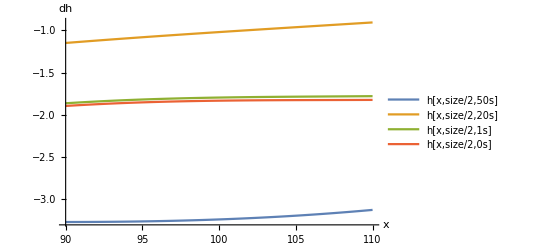

```mathematica
Plot[{scaleFun[plotFun[x,tMax],min50s,max50s,50000000],scaleFun[plotFun[x,20000000],min20s,max20s,20000000],scaleFun[plotFun[x,1000000],min1s,max1s,1000000],scaleFun[plotFun[x,1],min0s,max0s,1]},{x,xMin,xMax},AxesLabel->{"x","dh"},PlotLegends->{"h[x,size/2,50s]","h[x,size/2,20s]","h[x,size/2,1s]","h[x,size/2,0s]"},PlotRange->Full]
```

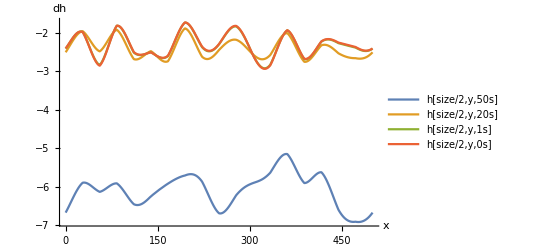

```mathematica
Plot[{scaleFunNotEntireDomain[plotFunYCut[y,tMax],min50s,max50s,50000000],scaleFunNotEntireDomain[plotFunYCut[y,20000000],min20s,max20s,20000000],scaleFunNotEntireDomain[plotFunYCut[y,1000000],min1s,max1s,1000000],scaleFunNotEntireDomain[plotFunYCut[y,1],min0s,max0s,1]},{y,0,size},AxesLabel->{"x","dh"},PlotLegends->{"h[size/2,y,50s]","h[size/2,y,20s]","h[size/2,y,1s]","h[size/2,y,0s]"},PlotRange->Full]
```

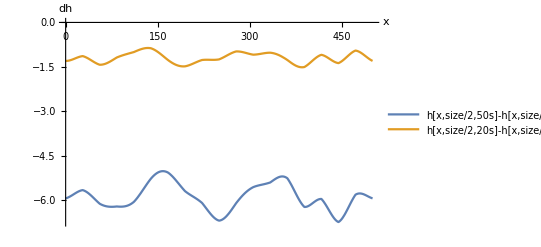

```mathematica
Plot[{diff[x,tMax],diff[x,20000000]},{x,0,size},AxesLabel->{"x","dh"},PlotLegends->{"h[x,size/2,50s]-h[x,size/2,0]","h[x,size/2,20s]-h[x,size/2,0]"}]
```

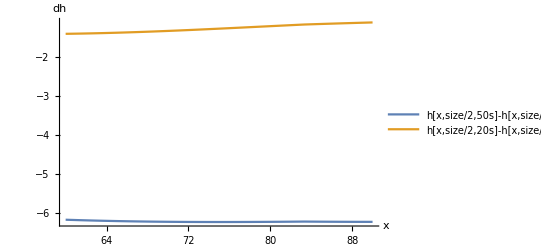

```mathematica
Plot[{diff[x,tMax],diff[x,20000000]},{x,60,90},AxesLabel->{"x","dh"},PlotLegends->{"h[x,size/2,50s]-h[x,size/2,0]","h[x,size/2,20s]-h[x,size/2,0]"}]
```

```mathematica
ffun[120,120,1000000]-ffun[120,120,0]
```

-0.061266319071588

```mathematica
SeedRandom[2]
```

```mathematica
(RandomInteger[{-5,5},1]⟦1⟧)/10
```

3/10

```mathematica
(RandomInteger[{-5,5},1]⟦1⟧)/10
```

-1/10

```mathematica
(RandomInteger[{-5,5},1]⟦1⟧)/10
```

0

```mathematica
(RandomInteger[{-5,5},1]⟦1⟧)/10
```

-1/10

```mathematica
(RandomInteger[{-5,5},1]⟦1⟧)/10
```

1/5

```mathematica
ffun[0,0,1000000]-ffun[0,0,0]
```

-0.0712787513337574

```mathematica
Table[{xVal,{ffun[x,y,t]/.{x->xVal,y->0,t->50000000}}},{xVal,0,size}]
```

{{0,{-3.17953831655839}},{1,{-3.19126717661264}},{2,{-3.20389182710032}},{3,{-3.21735415830284}},{4,{-3.23159197862931}},{5,{-3.24653931458635}},{6,{-3.26212672070911}},{7,{-3.27828159856502}},{8,{-3.29492852394211}},{9,{-3.31198958133371}},{10,{-3.32938470483106}},{11,{-3.34703202453587}},{12,{-3.36484821760432}},{13,{-3.38274886303439}},{14,{-3.40064879930818}},{15,{-3.41846248400106}},{16,{-3.4361043544693}},{17,{-3.45348918872799}},{18,{-3.47053246563095}},{19,{-3.48715072346438}},{20,{-3.50326191606609}},{21,{-3.51878576558186}},{22,{-3.53364411097088}},{23,{-3.54776125137189}},{24,{-3.5610642834418}},{25,{-3.57348343177852}},{26,{-3.5849523715398}},{27,{-3.59540854236977}},{28,{-3.60378835376404}},{29,{-3.60753900809233}},{30,{-3.61017315955745}},{31,{-3.61169354575128}},{32,{-3.61210729205716}},{33,{-3.6114258056154}},{34,{-3.60966465882055}},{35,{-3.60684346284053}},{36,{-3.60298573164803}},{37,{-3.59811873705427}},{38,{-3.59227335523535}},{39,{-3.58548390524159}},{40,{-3.57778797997983}},{41,{-3.56922627015916}},{42,{-3.55984238169018}},{43,{-3.54968264702799}},{44,{-3.53879593094933}},{45,{-3.52723343125383}},{46,{-3.51504847487981}},{47,{-3.50229630992481}},{48,{-3.48903389406102}},{49,{-3.47531967983589}},{50,{-3.46121339734818}},{51,{-3.44677583478956}},{52,{-3.43206861734218}},{53,{-3.41715398492223}},{54,{-3.402094569259944}},{55,{-3.386953170806001}},{56,{-3.37217810217422}},{57,{-3.35792405206777}},{58,{-3.34376198460171}},{59,{-3.32974410966053}},{60,{-3.31592187046256}},{61,{-3.30234579654109}},{62,{-3.28906535907281}},{63,{-3.27612882877906}},{64,{-3.263583136626}},{65,{-3.25147373754914}},{66,{-3.2398444774282}},{67,{-3.22873746353798}},{68,{-3.21819293870097}},{69,{-3.20824915936758}},{70,{-3.19894227784961}},{71,{-3.19030622893279}},{72,{-3.18237262109418}},{73,{-3.17517063255013}},{74,{-3.16872691236055}},{75,{-3.1630654868154}},{76,{-3.1582076713289}},{77,{-3.15417198806747}},{78,{-3.15097408953706}},{79,{-3.14862668835555}},{80,{-3.14713949343614}},{81,{-3.14651915280739}},{82,{-3.14676920329565}},{83,{-3.147890027295751}},{84,{-3.15163075475637}},{85,{-3.15709136998971}},{86,{-3.16335845300823}},{87,{-3.17039215892035}},{88,{-3.17814993330456}},{89,{-3.18658671820705}},{90,{-3.19565516386918}},{91,{-3.20530584560886}},{92,{-3.21548748528041}},{93,{-3.22614717673682}},{94,{-3.23723061471907}},{95,{-3.24868232659644}},{96,{-3.26044590638231}},{97,{-3.27246425044972}},{98,{-3.28467979437082}},{99,{-3.29703475030462}},{100,{-3.30947134435734}},{101,{-3.3219320533395}},{102,{-3.33435984034413}},{103,{-3.34669838857043}},{104,{-3.35889233281701}},{105,{-3.37088748806909}},{106,{-3.38263107460395}},{107,{-3.39407193903885}},{108,{-3.40516077074572}},{109,{-3.41585031305693}},{110,{-3.426095568686388}},{111,{-3.435853998790255}},{112,{-3.44222465049378}},{113,{-3.44770368650089}},{114,{-3.45264902895917}},{115,{-3.4570631795003}},{116,{-3.46095125251612}},{117,{-3.46432087717173}},{118,{-3.46718209284811}},{119,{-3.46954723842073}},{120,{-3.47143083578076}},{121,{-3.47284946800537}},{122,{-3.47382165258379}},{123,{-3.47436771010544}},{124,{-3.47450962881692}},{125,{-3.47427092545429}},{126,{-3.47367650275714}},{127,{-3.47275250407111}},{128,{-3.47152616544529}},{129,{-3.47002566563114}},{130,{-3.4682799743894}},{131,{-3.46631869951163}},{132,{-3.46417193296273}},{133,{-3.46187009655126}},{134,{-3.45944378753387}},{135,{-3.45692362456052}},{136,{-3.45434009436695}},{137,{-3.45172339962098}},{138,{-3.449103308329284}},{139,{-3.44668669801197}},{140,{-3.44574204408353}},{141,{-3.44486044850464}},{142,{-3.44405173160626}},{143,{-3.44332482742705}},{144,{-3.44268777461089}},{145,{-3.44214771019434}},{146,{-3.44171086620311}},{147,{-3.44138256897681}},{148,{-3.44116724114111}},{149,{-3.44106840614646}},{150,{-3.44108869529253}},{151,{-3.44122985715763}},{152,{-3.44149276935212}},{153,{-3.44187745251512}},{154,{-3.44238308647367}},{155,{-3.44300802848334}},{156,{-3.44374983346974}},{157,{-3.44460527618984}},{158,{-3.44557037523241}},{159,{-3.44664041877675}},{160,{-3.44780999202875}},{161,{-3.44907300625361}},{162,{-3.45042272932428}},{163,{-3.45185181770486}},{164,{-3.45335234978803}},{165,{-3.454915860505767}},{166,{-3.45653337713251}},{167,{-3.45822466819165}},{168,{-3.46000872604916}},{169,{-3.46181596642837}},{170,{-3.46363484968988}},{171,{-3.46545353857375}},{172,{-3.46725994621738}},{173,{-3.46904178471088}},{174,{-3.47078661408255}},{175,{-3.47248189160674}},{176,{-3.47411502132667}},{177,{-3.47567340368465}},{178,{-3.4771444851521}},{179,{-3.47851580775186}},{180,{-3.47977505836526}},{181,{-3.48091011771637}},{182,{-3.48190910892595}},{183,{-3.48276044552745}},{184,{-3.4834528788376}},{185,{-3.48397554457406}},{186,{-3.48431800861246}},{187,{-3.48447031177549}},{188,{-3.48442301354622}},{189,{-3.48416723459845}},{190,{-3.48369469803619}},{191,{-3.482997769235}},{192,{-3.48206949417748}},{193,{-3.48090363617545}},{194,{-3.479494710871278}},{195,{-3.47745134788258}},{196,{-3.47485102942378}},{197,{-3.47200745055317}},{198,{-3.46892569670995}},{199,{-3.46561161228052}},{200,{-3.4620717694666}},{201,{-3.45831343543427}},{202,{-3.45434453784862}},{203,{-3.45017362889853}},{204,{-3.44580984791646}},{205,{-3.44126288269783}},{206,{-3.43654292962461}},{207,{-3.43166065269795}},{208,{-3.42662714158437}},{209,{-3.42145386878034}},{210,{-3.41615264599976}},{211,{-3.41073557988923}},{212,{-3.40521502717556}},{213,{-3.39960354935037}},{214,{-3.39391386699638}},{215,{-3.38815881386014}},{216,{-3.38235129077575}},{217,{-3.37650421954434}},{218,{-3.37063049687408}},{219,{-3.36474294848516}},{220,{-3.35885428348462}},{221,{-3.35297704911567}},{222,{-3.347123585986085}},{223,{-3.3414294266446}},{224,{-3.33581692161264}},{225,{-3.33026055547962}},{226,{-3.32476976003183}},{227,{-3.31935358181082}},{228,{-3.3140206545983}},{229,{-3.30877917292992}},{230,{-3.30363686669436}},{231,{-3.29860097687391}},{232,{-3.29367823248279}},{233,{-3.28887482875951}},{234,{-3.28419640666949}},{235,{-3.27964803377429}},{236,{-3.27523418652356}},{237,{-3.27095873402607}},{238,{-3.26682492335613}},{239,{-3.26283536645152}},{240,{-3.25899202865926}},{241,{-3.25529621898557}},{242,{-3.25174858210608}},{243,{-3.24834909219275}},{244,{-3.24509704861365}},{245,{-3.24199107356183}},{246,{-3.23902911166971}},{247,{-3.23620843166498}},{248,{-3.2335256301246}},{249,{-3.23097663738283}},{250,{-3.2285567256498}},{251,{-3.22778197266097}},{252,{-3.22710881294058}},{253,{-3.22651463364432}},{254,{-3.22597645766412}},{255,{-3.22547108155977}},{256,{-3.2249752146453}},{257,{-3.22446561882153}},{258,{-3.22391924874686}},{259,{-3.22331339193791}},{260,{-3.22262580839181}},{261,{-3.22183486932201}},{262,{-3.2209196945993}},{263,{-3.21986028848979}},{264,{-3.21863767328178}},{265,{-3.21723402039311}},{266,{-3.21563277855094}},{267,{-3.2138187986356}},{268,{-3.21177845478038}},{269,{-3.20949976131899}},{270,{-3.20697248517252}},{271,{-3.20418825326758}},{272,{-3.20114065457755}},{273,{-3.19782533637854}},{274,{-3.19424009431203}},{275,{-3.19038495584581}},{276,{-3.18626225672504}},{277,{-3.181876710005294}},{278,{-3.17620529231938}},{279,{-3.16669663925965}},{280,{-3.15701393836439}},{281,{-3.14722042550038}},{282,{-3.13738112901545}},{283,{-3.12756252782545}},{284,{-3.11783220377824}},{285,{-3.10825848929926}},{286,{-3.09891011132344}},{287,{-3.08985583251802}},{288,{-3.08116409080093}},{289,{-3.07290263815955}},{290,{-3.06513817977425}},{291,{-3.05793601445154}},{292,{-3.05135967737149}},{293,{-3.04547058615395}},{294,{-3.04032769124838}},{295,{-3.03598713165181}},{296,{-3.03250189695968}},{297,{-3.02992149675418}},{298,{-3.02829163833474}},{299,{-3.02765391379532}},{300,{-3.02804549745323}},{301,{-3.02949885463398}},{302,{-3.03204146281703}},{303,{-3.03569554614686}},{304,{-3.04047782431421}},{305,{-3.046399276812081}},{306,{-3.05726932422973}},{307,{-3.07399674775261}},{308,{-3.09172924544809}},{309,{-3.11036354218395}},{310,{-3.12979134293272}},{311,{-3.14989986969502}},{312,{-3.17057241184185}},{313,{-3.19168888827085}},{314,{-3.21312641977186}},{315,{-3.23475990999673}},{316,{-3.2564626334285}},{317,{-3.27810682874526}},{318,{-3.29956429597358}},{319,{-3.32070699582672}},{320,{-3.34140764962283}},{321,{-3.36154033817811}},{322,{-3.38098109807016}},{323,{-3.39960851366655}},{324,{-3.41730430331388}},{325,{-3.43395389808225}},{326,{-3.44944701146041}},{327,{-3.46367819839668}},{328,{-3.47654740208074}},{329,{-3.48796048686137}},{330,{-3.49782975569539}},{331,{-3.50607445052277}},{332,{-3.51262123396312}},{333,{-3.51740465072868}},{334,{-3.51291420354639}},{335,{-3.50290484191718}},{336,{-3.49118388928914}},{337,{-3.47783782947107}},{338,{-3.462960648624}},{339,{-3.44665328207453}},{340,{-3.42902304211313}},{341,{-3.41018302858219}},{342,{-3.39025152405872}},{343,{-3.3693513754367}},{344,{-3.34760936371394}},{345,{-3.3251555637883}},{346,{-3.30212269606826}},{347,{-3.27864547170276}},{348,{-3.25485993323507}},{349,{-3.23090279248581}},{350,{-3.20691076746984}},{351,{-3.18301992015205}},{352,{-3.15936499684689}},{353,{-3.13607877306658}},{354,{-3.1132914046229}},{355,{-3.09112978678744}},{356,{-3.06971692331529}},{357,{-3.04917130713696}},{358,{-3.02960631452358}},{359,{-3.01112961453016}},{360,{-2.99384259552188}},{361,{-2.97783981058833}},{362,{-2.9731896776013}},{363,{-2.97113401348723}},{364,{-2.97037633295384}},{365,{-2.97086234985753}},{366,{-2.97253104710606}},{367,{-2.97531513428371}},{368,{-2.97914152347226}},{369,{-2.98393182164618}},{370,{-2.98960283801992}},{371,{-2.99606710472558}},{372,{-3.00323340919909}},{373,{-3.01100733665293}},{374,{-3.01929182101363}},{375,{-3.02798770270213}},{376,{-3.03699429163519}},{377,{-3.04620993382588}},{378,{-3.05553257996142}},{379,{-3.06486035433637}},{380,{-3.0740921225194}},{381,{-3.08312805613173}},{382,{-3.09187019311539}},{383,{-3.10022299186945}},{384,{-3.10809387763226}},{385,{-3.115393779488}},{386,{-3.12203765637554}},{387,{-3.12794501047775}},{388,{-3.13304038636948}},{389,{-3.13617129871682}},{390,{-3.12971924978073}},{391,{-3.12237818948572}},{392,{-3.11419951874431}},{393,{-3.10524029967434}},{394,{-3.09556288228682}},{395,{-3.08523451481692}},{396,{-3.07432693904552}},{397,{-3.06291597195877}},{398,{-3.0510810750929}},{399,{-3.03890491291168}},{400,{-3.02647290156406}},{401,{-3.01387274936912}},{402,{-3.00119399037589}},{403,{-2.98852751234533}},{404,{-2.97596508050187}},{405,{-2.96359885840187}},{406,{-2.95152092726639}},{407,{-2.93982280512559}},{408,{-2.92859496712227}},{409,{-2.91792636832171}},{410,{-2.9079039703754}},{411,{-2.8986122733859}},{412,{-2.8901328543202}},{413,{-2.88254391331909}},{414,{-2.87591982924972}},{415,{-2.87033072584889}},{416,{-2.86584204980431}},{417,{-2.86501927700874}},{418,{-2.87039295835182}},{419,{-2.87692555372851}},{420,{-2.88458137259046}},{421,{-2.89331953299651}},{422,{-2.90309421912886}},{423,{-2.91385495254302}},{424,{-2.92554687620819}},{425,{-2.93811105039475}},{426,{-2.95148475946543}},{427,{-2.96560182862686}},{428,{-2.98039294969801}},{429,{-2.99578601495229}},{430,{-3.01170645808978}},{431,{-3.0280776013964}},{432,{-3.04482100814648}},{433,{-3.0618568393054}},{434,{-3.07910421358901}},{435,{-3.09648156993642}},{436,{-3.11390703145263}},{437,{-3.13129876987791}},{438,{-3.14857536964033}},{439,{-3.16565619054817}},{440,{-3.18246172817877}},{441,{-3.19891397102053}},{442,{-3.21493675342467}},{443,{-3.23045610342323}},{444,{-3.245400584470239}},{445,{-3.25755725463907}},{446,{-3.26731196894495}},{447,{-3.27635937826162}},{448,{-3.28468164959611}},{449,{-3.29226430009265}},{450,{-3.29909618553035}},{451,{-3.30516948032485}},{452,{-3.31047964926761}},{453,{-3.31502541123637}},{454,{-3.31880869511028}},{455,{-3.32183458812337}},{456,{-3.32411127688988}},{457,{-3.32564998133495}},{458,{-3.3264648817643}},{459,{-3.32657303930652}},{460,{-3.32599430996136}},{461,{-3.32475125248774}},{462,{-3.322869030365}},{463,{-3.32037530806089}},{464,{-3.31730014183997}},{465,{-3.31367586534587}},{466,{-3.3095369701911}},{467,{-3.30491998178782}},{468,{-3.29986333065328}},{469,{-3.29440721942337}},{470,{-3.28859348580799}},{471,{-3.2824654617216}},{472,{-3.276067828822718}},{473,{-3.26862259812466}},{474,{-3.26077367100769}},{475,{-3.25281564728995}},{476,{-3.24480809704987}},{477,{-3.23681094254088}},{478,{-3.22888421577603}},{479,{-3.22108781537726}},{480,{-3.21348126324601}},{481,{-3.20612346161183}},{482,{-3.19907245101573}},{483,{-3.19238516978509}},{484,{-3.18611721555667}},{485,{-3.18032260940458}},{486,{-3.17505356312992}},{487,{-3.17036025026866}},{488,{-3.16629058137468}},{489,{-3.16288998413456}},{490,{-3.16020118887091}},{491,{-3.15826401999081}},{492,{-3.15711519393635}},{493,{-3.1567881241937}},{494,{-3.15731273391759}},{495,{-3.15871527672791}},{496,{-3.16101816623509}},{497,{-3.16423981485104}},{498,{-3.16839448244229}},{499,{-3.17349213538212}},{500,{-3.17953831655839}}}

```mathematica
Table[{xVal,{ffun[x,y,t]/.{x->xVal,y->50,t->50000000}}},{xVal,0,size}]
```

{{0,{-2.82286314774444}},{1,{-2.80480940746957}},{2,{-2.7868807823855}},{3,{-2.7691376186971}},{4,{-2.751639975104}},{5,{-2.7344474537461}},{6,{-2.7176190314654}},{7,{-2.7012128917069}},{8,{-2.6852862573786}},{9,{-2.6698952249928}},{10,{-2.6550946004109}},{11,{-2.6409377365122}},{12,{-2.627476373109}},{13,{-2.6147604794294}},{14,{-2.6028380994891}},{15,{-2.5917552006746}},{16,{-2.5815555258577}},{17,{-2.5722804493656}},{18,{-2.5639688371247}},{19,{-2.5566569113029}},{20,{-2.55037811977}},{21,{-2.5451630106987}},{22,{-2.541039112627}},{23,{-2.5380308203042}},{24,{-2.5361592866424}},{25,{-2.53544232109362}},{26,{-2.53589429477607}},{27,{-2.53752605266943}},{28,{-2.54090445397185}},{29,{-2.54742427105732}},{30,{-2.5551019858712}},{31,{-2.5639072745097}},{32,{-2.5738064022023}},{33,{-2.5847623790804}},{34,{-2.5967351227958}},{35,{-2.6096816275383}},{36,{-2.6235561390114}},{37,{-2.6383103349166}},{38,{-2.6538935105016}},{39,{-2.6702527687269}},{40,{-2.6873332146042}},{41,{-2.7050781532612}},{42,{-2.7234292912856}},{43,{-2.7423269409047}},{44,{-2.761710226552}},{45,{-2.781517293377}},{46,{-2.8016855172505}},{47,{-2.8221517158217}},{48,{-2.8428523601783}},{49,{-2.8637237866659}},{50,{-2.8847024084203}},{51,{-2.90572492616609}},{52,{-2.92672853783564}},{53,{-2.94765114656382}},{54,{-2.9684315666108}},{55,{-2.98900972676813}},{56,{-3.00877747733463}},{57,{-3.02754617214105}},{58,{-3.04595991186936}},{59,{-3.0639779443344}},{60,{-3.0815613596925}},{61,{-3.0986731741677}},{62,{-3.1152784094376}},{63,{-3.131344167609}},{64,{-3.1468397017152}},{65,{-3.1617364816652}},{66,{-3.1760082555758}},{67,{-3.1896311064174}},{68,{-3.2025835039054}},{69,{-3.2148463515661}},{70,{-3.2264030289104}},{71,{-3.2372394286438}},{72,{-3.2473439888459}},{73,{-3.2567077200486}},{74,{-3.2653242271443}},{75,{-3.2731897260561}},{76,{-3.2803030550989}},{77,{-3.2866656809644}},{78,{-3.29228169925924}},{79,{-3.29715782952811}},{80,{-3.30130340469264}},{81,{-3.30473035483659}},{82,{-3.30745318526853}},{83,{-3.30948894879295}},{84,{-3.30935744021104}},{85,{-3.30784601291152}},{86,{-3.30575315101896}},{87,{-3.303129095398}},{88,{-3.3000259383548}},{89,{-3.2964973868186}},{90,{-3.2925985217647}},{91,{-3.2883855544937}},{92,{-3.2839155803861}},{93,{-3.279246330748}},{94,{-3.2744359233658}},{95,{-3.2695426123853}},{96,{-3.2646245381353}},{97,{-3.2597394775086}},{98,{-3.2549445955214}},{99,{-3.2502961986653}},{100,{-3.2458494906707}},{101,{-3.2416583312969}},{102,{-3.2377749987681}},{103,{-3.2342499564704}},{104,{-3.2311316245277}},{105,{-3.2284661568733}},{106,{-3.22629722443465}},{107,{-3.22466580504769}},{108,{-3.223609980718}},{109,{-3.22316474284594}},{110,{-3.2233618060327}},{111,{-3.22422943108423}},{112,{-3.23020518677702}},{113,{-3.23740268287737}},{114,{-3.2452342903607}},{115,{-3.2536614303821}},{116,{-3.2626424637942}},{117,{-3.2721329629552}},{118,{-3.2820859911621}},{119,{-3.2924523888106}},{120,{-3.3031810653844}},{121,{-3.3142192963763}},{122,{-3.3255130242413}},{123,{-3.3370071624855}},{124,{-3.3486459019917}},{125,{-3.3603730186843}},{126,{-3.3721321816349}},{127,{-3.3838672607108}},{128,{-3.395522632869}},{129,{-3.407043486196}},{130,{-3.4183761207978}},{131,{-3.4294682456392}},{132,{-3.4402692704376}},{133,{-3.45073059171}},{134,{-3.46080587207767}},{135,{-3.47045131192935}},{136,{-3.47962591254475}},{137,{-3.48829172978119}},{138,{-3.49641411742454}},{139,{-3.50316598540021}},{140,{-3.50296530387451}},{141,{-3.5022233687273}},{142,{-3.5009959457965}},{143,{-3.4993419478961}},{144,{-3.4973230436701}},{145,{-3.4950032566178}},{146,{-3.4924485555741}},{147,{-3.4897264379311}},{148,{-3.4869055068859}},{149,{-3.484055043999}},{150,{-3.4812445783503}},{151,{-3.4785434535755}},{152,{-3.4760203940699}},{153,{-3.4737430716444}},{154,{-3.4717776739178}},{155,{-3.4701884757323}},{156,{-3.4690374148757}},{157,{-3.4683836733969}},{158,{-3.4682832657985}},{159,{-3.4687886353932}},{160,{-3.4699482601077}},{161,{-3.4718062690198}},{162,{-3.47440207091514}},{163,{-3.47776999614592}},{164,{-3.48193895307987}},{165,{-3.48693210042251}},{166,{-3.49276653669875}},{167,{-3.50280617104025}},{168,{-3.52036887463569}},{169,{-3.5386433924842}},{170,{-3.5575147966924}},{171,{-3.5768626814342}},{172,{-3.5965617580682}},{173,{-3.6164824661894}},{174,{-3.6364915988347}},{175,{-3.6564529400604}},{176,{-3.6762279131122}},{177,{-3.6956762374043}},{178,{-3.714656592529}},{179,{-3.7330272875139}},{180,{-3.7506469335469}},{181,{-3.7673751183863}},{182,{-3.7830730806777}},{183,{-3.7976043823935}},{184,{-3.8108355776162}},{185,{-3.8226368758836}},{186,{-3.8328827983145}},{187,{-3.8414528247349}},{188,{-3.8482320300225}},{189,{-3.8531117078892}},{190,{-3.85598998032037}},{191,{-3.85677239088937}},{192,{-3.85537248016724}},{193,{-3.85171234144551}},{194,{-3.84572315499166}},{195,{-3.8313213820033}},{196,{-3.8097255355921}},{197,{-3.7858316730225}},{198,{-3.7597251067239}},{199,{-3.7315003603384}},{200,{-3.7012607024731}},{201,{-3.6691176582737}},{202,{-3.6351905003436}},{203,{-3.5996057205369}},{204,{-3.5624964841472}},{205,{-3.5240020680203}},{206,{-3.4842672841145}},{207,{-3.4434418900352}},{208,{-3.4016799880674}},{209,{-3.3591394142339}},{210,{-3.315981118902}},{211,{-3.2723685404659}},{212,{-3.2284669736301}},{213,{-3.1844429338172}},{214,{-3.1404635192289}},{215,{-3.0966957720818}},{216,{-3.0533060405466}},{217,{-3.0104593429136}},{218,{-2.9683187355123}},{219,{-2.9270446859075}},{220,{-2.88679445290046}},{221,{-2.847721474858}},{222,{-2.80997476789635}},{223,{-2.7780942096833}},{224,{-2.7490330229973}},{225,{-2.7216068059464}},{226,{-2.6958824383783}},{227,{-2.6719207949319}},{228,{-2.6497766682335}},{229,{-2.6294987061122}},{230,{-2.6111293626337}},{231,{-2.5947048627559}},{232,{-2.5802551804044}},{233,{-2.5678040297723}},{234,{-2.557368869643}},{235,{-2.5489609205383}},{236,{-2.5425851944928}},{237,{-2.5382405372557}},{238,{-2.5359196827206}},{239,{-2.5356093193857}},{240,{-2.5372901686438}},{241,{-2.5409370747056}},{242,{-2.5465191059544}},{243,{-2.5539996675364}},{244,{-2.5633366249857}},{245,{-2.5744824386861}},{246,{-2.5873843089698}},{247,{-2.6019843316563}},{248,{-2.61821966382977}},{249,{-2.6360226996586}},{250,{-2.65532125605642}},{251,{-2.6789808376701}},{252,{-2.7039474964392}},{253,{-2.7301056214943}},{254,{-2.7573363223307}},{255,{-2.7855178887169}},{256,{-2.8145262565585}},{257,{-2.8442354786181}},{258,{-2.8745181989971}},{259,{-2.9052461302805}},{260,{-2.9362905322476}},{261,{-2.9675226910529}},{262,{-2.998814397779}},{263,{-3.0300384252648}},{264,{-3.0610690021121}},{265,{-3.0917822827736}},{266,{-3.1220568126247}},{267,{-3.1517739869233}},{268,{-3.1808185025585}},{269,{-3.2090788014942}},{270,{-3.2364475048068}},{271,{-3.262821836224}},{272,{-3.2881040340638}},{273,{-3.31220175048}},{274,{-3.33502843691444}},{275,{-3.35650371466143}},{276,{-3.37655372944492}},{277,{-3.3951114889133}},{278,{-3.41030099021029}},{279,{-3.41755486392553}},{280,{-3.423265245766}},{281,{-3.4274810662726}},{282,{-3.430258092526}},{283,{-3.4316585091913}},{284,{-3.4317504828265}},{285,{-3.4306077108488}},{286,{-3.4283089565524}},{287,{-3.4249375715719}},{288,{-3.4205810071845}},{289,{-3.415330315846}},{290,{-3.4092796443537}},{291,{-3.4025257200296}},{292,{-3.395167331319}},{293,{-3.3873048041975}},{294,{-3.3790394757805}},{295,{-3.3704731665285}},{296,{-3.3617076524437}},{297,{-3.3528441386494}},{298,{-3.3439827357482}},{299,{-3.3352219403514}},{300,{-3.3266581211747}},{301,{-3.3183850120923}},{302,{-3.31049321354553}},{303,{-3.30306970369788}},{304,{-3.29619736073141}},{305,{-3.289954497678}},{306,{-3.28768778269133}},{307,{-3.2902479732718}},{308,{-3.2935284802482}},{309,{-3.2975081866224}},{310,{-3.3021607264776}},{311,{-3.3074546915816}},{312,{-3.3133538525481}},{313,{-3.3198173937043}},{314,{-3.3268001608146}},{315,{-3.3342529208074}},{316,{-3.3421226326548}},{317,{-3.3503527285534}},{318,{-3.3588834045543}},{319,{-3.3676519197915}},{320,{-3.3765929034573}},{321,{-3.3856386686725}},{322,{-3.3947195324009}},{323,{-3.4037641405562}},{324,{-3.4126997974495}},{325,{-3.4214527987272}},{326,{-3.4299487669462}},{327,{-3.4381129889364}},{328,{-3.4458707540986}},{329,{-3.4531476927859}},{330,{-3.45987011391742}},{331,{-3.46596534097393}},{332,{-3.47136204552208}},{333,{-3.47599057741738}},{334,{-3.47797117813673}},{335,{-3.4781632225338}},{336,{-3.4774392400233}},{337,{-3.4757677649537}},{338,{-3.4731200157431}},{339,{-3.4694699783779}},{340,{-3.4647944836684}},{341,{-3.4590732782407}},{342,{-3.4522890892416}},{343,{-3.4444276827331}},{344,{-3.4354779157567}},{345,{-3.4254317820421}},{346,{-3.4142844513402}},{347,{-3.4020343023564}},{348,{-3.3886829492628}},{349,{-3.3742352617667}},{350,{-3.3586993787122}},{351,{-3.3420867151935}},{352,{-3.3244119631571}},{353,{-3.3056930854702}},{354,{-3.2859513034335}},{355,{-3.2652110777148}},{356,{-3.2435000826831}},{357,{-3.2208491741181}},{358,{-3.197292350275}},{359,{-3.17286670628091}},{360,{-3.14761238184067}},{361,{-3.12157250222995}},{362,{-3.0929617126698}},{363,{-3.0634504457449}},{364,{-3.0333412622418}},{365,{-3.0027098609347}},{366,{-2.9716340652997}},{367,{-2.9401935657838}},{368,{-2.9084696576484}},{369,{-2.876544974995}},{370,{-2.8445032215786}},{371,{-2.8124288990158}},{372,{-2.7804070329937}},{373,{-2.7485228980847}},{374,{-2.7168617417768}},{375,{-2.6855085083215}},{376,{-2.6545475630091}},{377,{-2.6240624174761}},{378,{-2.5941354566512}},{379,{-2.5648476679465}},{380,{-2.5362783732999}},{381,{-2.5085049646762}},{382,{-2.481602643631}},{383,{-2.4556441655458}},{384,{-2.4306995891404}},{385,{-2.406836031867}},{386,{-2.3841174317954}},{387,{-2.362604316593}},{388,{-2.34235358020733}},{389,{-2.3238193661997}},{390,{-2.3098497094891}},{391,{-2.2972468438859}},{392,{-2.2860132647991}},{393,{-2.276147449325}},{394,{-2.2676439708529}},{395,{-2.2604936221946}},{396,{-2.2546835467438}},{397,{-2.2501973771726}},{398,{-2.2470153811697}},{399,{-2.245114613728}},{400,{-2.2444690754864}},{401,{-2.2450498766336}},{402,{-2.2468254058787}},{403,{-2.2497615039955}},{404,{-2.2538216414469}},{405,{-2.2589670995944}},{406,{-2.2651571550011}},{407,{-2.2723492663319}},{408,{-2.280499263359}},{409,{-2.2895615375777}},{410,{-2.2994892339399}},{411,{-2.3102344432104}},{412,{-2.3217483944524}},{413,{-2.3339816471488}},{414,{-2.346884282466}},{415,{-2.36040609316469}},{416,{-2.37449677166544}},{417,{-2.388314472292}},{418,{-2.4010269224524}},{419,{-2.4141919847884}},{420,{-2.4277855817069}},{421,{-2.441783998019}},{422,{-2.4561638644336}},{423,{-2.4709021381624}},{424,{-2.4859760808652}},{425,{-2.5013632341659}},{426,{-2.5170413929701}},{427,{-2.5329885768127}},{428,{-2.5491829994671}},{429,{-2.5656030370461}},{430,{-2.5822271948228}},{431,{-2.5990340730041}},{432,{-2.6160023316849}},{433,{-2.6331106552141}},{434,{-2.6503377162022}},{435,{-2.6676621394002}},{436,{-2.6850624656815}},{437,{-2.7025171163539}},{438,{-2.7200043580351}},{439,{-2.7375022683196}},{440,{-2.7549887024677}},{441,{-2.7724412613472}},{442,{-2.78983726085654}},{443,{-2.80715370306155}},{444,{-2.82436724927372}},{445,{-2.84241656651404}},{446,{-2.8610750583378}},{447,{-2.8795299255031}},{448,{-2.8977382031366}},{449,{-2.9156568336802}},{450,{-2.9332427897327}},{451,{-2.9504531985678}},{452,{-2.9672454680286}},{453,{-2.9835774135013}},{454,{-2.9994073856694}},{455,{-3.0146943987504}},{456,{-3.0293982589179}},{457,{-3.0434796926091}},{458,{-3.0569004744215}},{459,{-3.0696235542992}},{460,{-3.0816131837119}},{461,{-3.0928350405278}},{462,{-3.1032563522818}},{463,{-3.1128460175426}},{464,{-3.1215747250789}},{465,{-3.1294150705267}},{466,{-3.1363416702615}},{467,{-3.1423312721746}},{468,{-3.1473628630572}},{469,{-3.15141777229365}},{470,{-3.154479771566}},{471,{-3.15653517027104}},{472,{-3.15757290635265}},{473,{-3.1563751148128}},{474,{-3.1538126431698}},{475,{-3.1502450869641}},{476,{-3.1456888501003}},{477,{-3.1401630029456}},{478,{-3.1336892200163}},{479,{-3.1262917127853}},{480,{-3.1179971577859}},{481,{-3.1088346201883}},{482,{-3.0988354730267}},{483,{-3.0880333122503}},{484,{-3.0764638677775}},{485,{-3.0641649107278}},{486,{-3.0511761570085}},{487,{-3.0375391674321}},{488,{-3.0232972445413}},{489,{-3.0084953263166}},{490,{-2.993179876945}},{491,{-2.9773987748237}},{492,{-2.9612011979769}},{493,{-2.9446375070612}},{494,{-2.9277591261362}},{495,{-2.9106184213759}},{496,{-2.893268577899}},{497,{-2.8757634748916}},{498,{-2.85815755920208}},{499,{-2.84050571758086}},{500,{-2.82286314774444}}}

```mathematica
Table[{xVal,{ffun[x,y,t]/.{x->xVal,y->100,t->50000000}}},{xVal,0,size}]
```

{{0,{-2.89029201859468}},{1,{-2.8833832080432}},{2,{-2.8764665514825}},{3,{-2.8695626497941}},{4,{-2.8626916508947}},{5,{-2.85587319102}},{6,{-2.849126337554}},{7,{-2.84246953349}},{8,{-2.835920543608}},{9,{-2.8294964024551}},{10,{-2.8232133642126}},{11,{-2.8170868545372}},{12,{-2.8111314244605}},{13,{-2.8053607064324}},{14,{-2.799787372595}},{15,{-2.7944230953705}},{16,{-2.7892785104505}},{17,{-2.7843631822711}},{18,{-2.7796855720596}},{19,{-2.7752530085379}},{20,{-2.7710716613688}},{21,{-2.7671465174302}},{22,{-2.7634813600023}},{23,{-2.7600787509546}},{24,{-2.756940016016}},{25,{-2.754065233216}},{26,{-2.75145322458061}},{27,{-2.74910155116912}},{28,{-2.74734852687962}},{29,{-2.7470394374133}},{30,{-2.7469559406685}},{31,{-2.7470744768277}},{32,{-2.7473705204648}},{33,{-2.7478187162323}},{34,{-2.7483930169757}},{35,{-2.7490668238921}},{36,{-2.7498131283496}},{37,{-2.7506046549826}},{38,{-2.7514140056819}},{39,{-2.7522138040932}},{40,{-2.7529768402422}},{41,{-2.7536762149026}},{42,{-2.7542854833219}},{43,{-2.7547787979239}},{44,{-2.7551310496019}},{45,{-2.7553180072203}},{46,{-2.755316454941}},{47,{-2.7551043269902}},{48,{-2.7546608394832}},{49,{-2.7539666189219}},{50,{-2.7530038269841}},{51,{-2.7517562812173}},{52,{-2.7502095712571}},{53,{-2.7483511701841}},{54,{-2.74617054063681}},{55,{-2.74365923529666}},{56,{-2.7394461678873}},{57,{-2.7332009146565}},{58,{-2.7266599100389}},{59,{-2.7198559744912}},{60,{-2.7128238371726}},{61,{-2.7055999580765}},{62,{-2.698222345074}},{63,{-2.6907303664213}},{64,{-2.6831645592844}},{65,{-2.675566434832}},{66,{-2.6679782804513}},{67,{-2.6604429596374}},{68,{-2.6530037101105}},{69,{-2.6457039407117}},{70,{-2.6385870276316}},{71,{-2.6316961105235}},{72,{-2.6250738890533}},{73,{-2.6187624204402}},{74,{-2.6128029185389}},{75,{-2.6072355550172}},{76,{-2.6020992631811}},{77,{-2.597431545}},{78,{-2.5932682818844}},{79,{-2.5896435497693}},{80,{-2.5865894390547}},{81,{-2.5841358799574}},{82,{-2.5823104738249}},{83,{-2.58113833096541}},{84,{-2.5832558455009}},{85,{-2.5873488366671}},{86,{-2.5920850244136}},{87,{-2.5974373104548}},{88,{-2.6033762275607}},{89,{-2.6098701294083}},{90,{-2.6168853864313}},{91,{-2.6243865870257}},{92,{-2.6323367434677}},{93,{-2.6406975019002}},{94,{-2.649429355746}},{95,{-2.6584918619025}},{96,{-2.6678438590762}},{97,{-2.6774436876135}},{98,{-2.6872494101836}},{99,{-2.6972190326713}},{100,{-2.7073107246361}},{101,{-2.7174830386941}},{102,{-2.7276951281797}},{103,{-2.7379069624437}},{104,{-2.7480795391447}},{105,{-2.7581750928906}},{106,{-2.7681572995865}},{107,{-2.7779914758463}},{108,{-2.7876447728241}},{109,{-2.79708636382296}},{110,{-2.80628762503738}},{111,{-2.81522230878561}},{112,{-2.8194678934608}},{113,{-2.8228981258916}},{114,{-2.8260974755408}},{115,{-2.8291020543228}},{116,{-2.8319499659518}},{117,{-2.8346810411667}},{118,{-2.8373365668173}},{119,{-2.8399590096778}},{120,{-2.8425917358552}},{121,{-2.8452787266586}},{122,{-2.8480642917973}},{123,{-2.8509927807744}},{124,{-2.8541082933422}},{125,{-2.857454389888}},{126,{-2.8610738026146}},{127,{-2.8650081483853}},{128,{-2.8692976440984}},{129,{-2.8739808254592}},{130,{-2.8790942700151}},{131,{-2.8846723253234}},{132,{-2.890746843115}},{133,{-2.8973469203248}},{134,{-2.9044986478528}},{135,{-2.9122248679245}},{136,{-2.9205449409168}},{137,{-2.92947452251669}},{138,{-2.93902535207994}},{139,{-2.9499872099801}},{140,{-2.967821659704}},{141,{-2.9862045391234}},{142,{-3.0050563375492}},{143,{-3.0242939288313}},{144,{-3.043830989137}},{145,{-3.0635784253226}},{146,{-3.0834448126213}},{147,{-3.1033368403673}},{148,{-3.1231597644803}},{149,{-3.1428178654297}},{150,{-3.1622149104009}},{151,{-3.1812546183864}},{152,{-3.1998411269215}},{153,{-3.2178794591877}},{154,{-3.2352759902049}},{155,{-3.251938910834}},{156,{-3.2677786883115}},{157,{-3.2827085220379}},{158,{-3.2966447933422}},{159,{-3.3095075079423}},{160,{-3.321220729825}},{161,{-3.3317130052659}},{162,{-3.3409177757118}},{163,{-3.3487737782461}},{164,{-3.3552254323599}},{165,{-3.36022321175024}},{166,{-3.36372399986634}},{167,{-3.3626677364827}},{168,{-3.3540369690621}},{169,{-3.3439492804071}},{170,{-3.3324851236245}},{171,{-3.3197311983745}},{172,{-3.3057799825884}},{173,{-3.2907292482031}},{174,{-3.2746815623988}},{175,{-3.2577437758264}},{176,{-3.2400264993116}},{177,{-3.2216435705211}},{178,{-3.2027115120799}},{179,{-3.183348982623}},{180,{-3.1636762222714}},{181,{-3.1438144940163}},{182,{-3.1238855225001}},{183,{-3.1040109316794}},{184,{-3.0843116828572}},{185,{-3.0649075145712}},{186,{-3.0459163858242}},{187,{-3.0274539241431}},{188,{-3.0096328799539}},{189,{-2.9925625887586}},{190,{-2.9763484426008}},{191,{-2.9610913723066}},{192,{-2.9468873419873}},{193,{-2.93382685729095}},{194,{-2.92199448888826}},{195,{-2.9162820309384}},{196,{-2.9157479301646}},{197,{-2.9165133262253}},{198,{-2.9185444041577}},{199,{-2.9218010400681}},{200,{-2.926237113876}},{201,{-2.9318008383059}},{202,{-2.9384351029715}},{203,{-2.9460778323966}},{204,{-2.954662356818}},{205,{-2.964117794614}},{206,{-2.9743694452048}},{207,{-2.9853391912671}},{208,{-2.9969459091103}},{209,{-3.0091058860564}},{210,{-3.0217332436703}},{211,{-3.0347403656834}},{212,{-3.0480383294566}},{213,{-3.0615373398268}},{214,{-3.0751471641806}},{215,{-3.0887775676022}},{216,{-3.1023387469372}},{217,{-3.1157417626193}},{218,{-3.1288989671039}},{219,{-3.1417244287518}},{220,{-3.1541343500106}},{221,{-3.16604747873533}},{222,{-3.17738551149506}},{223,{-3.1839970088274}},{224,{-3.1887644977316}},{225,{-3.1928418390729}},{226,{-3.196220772647}},{227,{-3.1988967069176}},{228,{-3.2008686476415}},{229,{-3.2021391164311}},{230,{-3.2027140596991}},{231,{-3.2026027484287}},{232,{-3.201817669213}},{233,{-3.2003744070073}},{234,{-3.1982915200372}},{235,{-3.1955904073075}},{236,{-3.1922951691538}},{237,{-3.188432461282}},{238,{-3.1840313427378}},{239,{-3.1791231182515}},{240,{-3.1737411753997}},{241,{-3.1679208170296}},{242,{-3.1616990893879}},{243,{-3.1551146063986}},{244,{-3.1482073705332}},{245,{-3.1410185907169}},{246,{-3.1335904977146}},{247,{-3.1259661574396}},{248,{-3.1181892826298}},{249,{-3.11030404333369}},{250,{-3.10235487665084}},{251,{-3.0948777375374}},{252,{-3.0874203833218}},{253,{-3.0800217474704}},{254,{-3.0727203478004}},{255,{-3.0655541372323}},{256,{-3.0585603560084}},{257,{-3.0517753856696}},{258,{-3.0452346050857}},{259,{-3.0389722488316}},{260,{-3.0330212682031}},{261,{-3.0274131951669}},{262,{-3.0221780095368}},{263,{-3.0173440096707}},{264,{-3.0129376869822}},{265,{-3.0089836045592}},{266,{-3.0055042801842}},{267,{-3.0025200740495}},{268,{-3.0000490814604}},{269,{-2.9981070308214}},{270,{-2.9967071871964}},{271,{-2.9958602617399}},{272,{-2.9955743272893}},{273,{-2.9958547404144}},{274,{-2.9967040702167}},{275,{-2.9981220341721}},{276,{-3.0001054413101}},{277,{-3.00264814302455}},{278,{-3.006465202337}},{279,{-3.013344821942}},{280,{-3.0207051155061}},{281,{-3.0284936894047}},{282,{-3.0366556366786}},{283,{-3.0451337913713}},{284,{-3.053868989351}},{285,{-3.0628003349184}},{286,{-3.0718654724999}},{287,{-3.081000862727}},{288,{-3.0901420622029}},{289,{-3.0992240062546}},{290,{-3.1081812939727}},{291,{-3.1169484748392}},{292,{-3.1254603362419}},{293,{-3.1336521911776}},{294,{-3.1414601654434}},{295,{-3.1488214836172}},{296,{-3.1556747531261}},{297,{-3.1619602457056}},{298,{-3.1676201755472}},{299,{-3.172598973437}},{300,{-3.1768435561839}},{301,{-3.180303590639}},{302,{-3.1829317516052}},{303,{-3.1846839729393}},{304,{-3.18551969114453}},{305,{-3.18540208075577}},{306,{-3.1828020144686}},{307,{-3.177332941129}},{308,{-3.1708760292703}},{309,{-3.163446684101}},{310,{-3.1550644358259}},{311,{-3.1457528517791}},{312,{-3.1355394389871}},{313,{-3.1244555374872}},{314,{-3.1125362047284}},{315,{-3.0998200913827}},{316,{-3.0863493088909}},{317,{-3.0721692890721}},{318,{-3.0573286361218}},{319,{-3.0418789713264}},{320,{-3.02587477082}},{321,{-3.0093731967103}},{322,{-2.9924339219002}},{323,{-2.9751189489328}},{324,{-2.9574924231847}},{325,{-2.9396204407349}},{326,{-2.9215708512372}},{327,{-2.9034130561211}},{328,{-2.8852178024481}},{329,{-2.8670569727509}},{330,{-2.8490033711821}},{331,{-2.8311305062973}},{332,{-2.8135123708019}},{333,{-2.79622321858648}},{334,{-2.7781412693591}},{335,{-2.7599509588076}},{336,{-2.7423432416619}},{337,{-2.7254098005584}},{338,{-2.7092410619396}},{339,{-2.6939258258045}},{340,{-2.6795508970414}},{341,{-2.666200719216}},{342,{-2.6539570116892}},{343,{-2.6428984109385}},{344,{-2.6331001169563}},{345,{-2.6246335455995}},{346,{-2.6175659877641}},{347,{-2.6119602762585}},{348,{-2.6078744612489}},{349,{-2.6053614951519}},{350,{-2.6044689278469}},{351,{-2.6052386130823}},{352,{-2.6077064269503}},{353,{-2.6119019993031}},{354,{-2.6178484589841}},{355,{-2.6255621937499}},{356,{-2.6350526257539}},{357,{-2.6463220034682}},{358,{-2.659365210916}},{359,{-2.6741695950883}},{360,{-2.69071481242019}},{361,{-2.70897269519838}},{362,{-2.7371797062253}},{363,{-2.7679670971463}},{364,{-2.8001493036217}},{365,{-2.8335694865637}},{366,{-2.8680647418759}},{367,{-2.9034668183968}},{368,{-2.9396028508484}},{369,{-2.9762961058216}},{370,{-3.0133667388343}},{371,{-3.0506325604936}},{372,{-3.0879098097979}},{373,{-3.125013932611}},{374,{-3.1617603633427}},{375,{-3.1979653078697}},{376,{-3.2334465257294}},{377,{-3.2680241096216}},{378,{-3.3015212602513}},{379,{-3.3337650545459}},{380,{-3.3645872052807}},{381,{-3.3938248101469}},{382,{-3.4213210882949}},{383,{-3.4469261023875}},{384,{-3.4704974641956}},{385,{-3.4919010217713}},{386,{-3.5110115262311}},{387,{-3.5277132761834}},{388,{-3.54190073783396}},{389,{-3.552078164388}},{390,{-3.5483854812625}},{391,{-3.5420766739986}},{392,{-3.5332245746074}},{393,{-3.5219127704885}},{394,{-3.5082350628857}},{395,{-3.4922948992117}},{396,{-3.4742047811179}},{397,{-3.4540856501842}},{398,{-3.4320662531068}},{399,{-3.4082824882589}},{400,{-3.382876735502}},{401,{-3.3559971711222}},{402,{-3.3277970697694}},{403,{-3.2984340952758}},{404,{-3.2680695822276}},{405,{-3.2368678101698}},{406,{-3.204995272317}},{407,{-3.1726199406489}},{408,{-3.1399105292653}},{409,{-3.1070357578776}},{410,{-3.0741636173129}},{411,{-3.041460638907}},{412,{-3.0090911696628}},{413,{-2.9772166550493}},{414,{-2.9459949313196}},{415,{-2.9155795292217}},{416,{-2.88611899098064}},{417,{-2.8606942435362}},{418,{-2.8423453726146}},{419,{-2.8252364096412}},{420,{-2.8093973824717}},{421,{-2.7948517856822}},{422,{-2.7816166962361}},{423,{-2.769702906599}},{424,{-2.7591150744932}},{425,{-2.749851888479}},{426,{-2.7419062485556}},{427,{-2.7352654609673}},{428,{-2.7299114464089}},{429,{-2.7258209608165}},{430,{-2.7229658279354}},{431,{-2.7213131828536}},{432,{-2.7208257256916}},{433,{-2.7214619846376}},{434,{-2.7231765875167}},{435,{-2.7259205410864}},{436,{-2.7296415172455}},{437,{-2.7342841453469}},{438,{-2.7397903098048}},{439,{-2.7460994521848}},{440,{-2.7531488769668}},{441,{-2.760874060171}},{442,{-2.7692089600359}},{443,{-2.77808632893856}},{444,{-2.78743802574602}},{445,{-2.7958617350013}},{446,{-2.8035690809985}},{447,{-2.8115834838239}},{448,{-2.8198613319641}},{449,{-2.8283591815154}},{450,{-2.8370338694211}},{451,{-2.8458426240708}},{452,{-2.8547431731824}},{453,{-2.8636938488895}},{454,{-2.8726536899549}},{455,{-2.8815825410324}},{456,{-2.8904411488981}},{457,{-2.8991912555729}},{458,{-2.9077956882577}},{459,{-2.9162184460035}},{460,{-2.924424783037}},{461,{-2.9323812886642}},{462,{-2.9400559636726}},{463,{-2.9474182931553}},{464,{-2.9544393156762}},{465,{-2.9610916887002}},{466,{-2.9673497502086}},{467,{-2.9731895764215}},{468,{-2.9785890355494}},{469,{-2.9835278374948}},{470,{-2.987987579426}},{471,{-2.9919517871444}},{472,{-2.99540595216705}},{473,{-2.9976028785675}},{474,{-2.9990644263624}},{475,{-3.0000022173927}},{476,{-3.0004196955848}},{477,{-3.0003221842542}},{478,{-2.9997168233222}},{479,{-2.9986125027876}},{480,{-2.9970197926626}},{481,{-2.994950869584}},{482,{-2.9924194403076}},{483,{-2.9894406622981}},{484,{-2.9860310616216}},{485,{-2.982208448352}},{486,{-2.9779918297013}},{487,{-2.9734013210823}},{488,{-2.9684580553145}},{489,{-2.963184090183}},{490,{-2.9576023145589}},{491,{-2.9517363532932}},{492,{-2.9456104710914}},{493,{-2.9392494755806}},{494,{-2.9326786197778}},{495,{-2.92592350417}},{496,{-2.9190099786142}},{497,{-2.9119640442694}},{498,{-2.9048117557685}},{499,{-2.8975791238409}},{500,{-2.89029201859468}}}

```mathematica
Table[{xVal,{ffun[x,y,t]/.{x->xVal,y->150,t->50000000}}},{xVal,0,size}]
```

{{0,{-2.61242713221433}},{1,{-2.5930200315807}},{2,{-2.5745994442881}},{3,{-2.5572327131189}},{4,{-2.5409829848137}},{5,{-2.5259090882307}},{6,{-2.5120654233163}},{7,{-2.4995018608256}},{8,{-2.4882636527277}},{9,{-2.4783913532332}},{10,{-2.46992075038}},{11,{-2.4628828081143}},{12,{-2.4573036188029}},{13,{-2.4532043661137}},{14,{-2.4506012982003}},{15,{-2.4495057111284}},{16,{-2.4499239424789}},{17,{-2.4518573750661}},{18,{-2.4553024507053}},{19,{-2.4602506939685}},{20,{-2.4666887458635}},{21,{-2.4745984073728}},{22,{-2.48395669279}},{23,{-2.4947358927881}},{24,{-2.5069036471592}},{25,{-2.5204230271587}},{26,{-2.5352526273938}},{27,{-2.55134666719028}},{28,{-2.5692550601902}},{29,{-2.5904151101438}},{30,{-2.6126423185433}},{31,{-2.6358463671514}},{32,{-2.659933677744}},{33,{-2.6848077774348}},{34,{-2.7103696703844}},{35,{-2.7365182150052}},{36,{-2.7631505057791}},{37,{-2.790162258798}},{38,{-2.8174482001435}},{39,{-2.8449024562188}},{40,{-2.8724189451452}},{41,{-2.8998917683389}},{42,{-2.9272156013803}},{43,{-2.9542860832903}},{44,{-2.9810002033264}},{45,{-3.0072566844132}},{46,{-3.032956362321}},{47,{-3.058002559705}},{48,{-3.0823014541199}},{49,{-3.1057624391236}},{50,{-3.1282984775828}},{51,{-3.1498264462951}},{52,{-3.1702674710405}},{53,{-3.1895472511771}},{54,{-3.2075963728928}},{55,{-3.22435061022914}},{56,{-3.2372685552786}},{57,{-3.2457034144137}},{58,{-3.2527698022685}},{59,{-3.2584852402251}},{60,{-3.2628726623654}},{61,{-3.2659601942498}},{62,{-3.2677809191285}},{63,{-3.2683726324013}},{64,{-3.2677775851431}},{65,{-3.2660422175108}},{66,{-3.2632168828496}},{67,{-3.259355563314}},{68,{-3.2545155778204}},{69,{-3.2487572831487}},{70,{-3.2421437690085}},{71,{-3.234740547887}},{72,{-3.2266152404949}},{73,{-3.2178372576273}},{74,{-3.2084774792559}},{75,{-3.1986079316694}},{76,{-3.188301463478}},{77,{-3.1776314212995}},{78,{-3.1666713259428}},{79,{-3.1554945499067}},{80,{-3.1441739970081}},{81,{-3.1327817849593}},{82,{-3.12138893170855}},{83,{-3.11006504636164}},{84,{-3.1011100893472}},{85,{-3.0934509567974}},{86,{-3.0859992936987}},{87,{-3.0787812872066}},{88,{-3.071820964218}},{89,{-3.0651401842299}},{90,{-3.0587586387506}},{91,{-3.0526938570602}},{92,{-3.0469612181138}},{93,{-3.0415739683846}},{94,{-3.0365432454411}},{95,{-3.0318781070551}},{96,{-3.0275855656348}},{97,{-3.0236706277793}},{98,{-3.0201363387492}},{99,{-3.0169838316501}},{100,{-3.0142123811224}},{101,{-3.011819461335}},{102,{-3.0098008080773}},{103,{-3.0081504847442}},{104,{-3.0068609520118}},{105,{-3.0059231409969}},{106,{-3.0053265296973}},{107,{-3.0050592225074}},{108,{-3.0051080326057}},{109,{-3.00545856700836}},{110,{-3.00609531408526}},{111,{-3.00700173333348}},{112,{-3.0085325517089}},{113,{-3.0103398946236}},{114,{-3.0123537013895}},{115,{-3.0145499113901}},{116,{-3.0169040050827}},{117,{-3.0193911351295}},{118,{-3.021986257857}},{119,{-3.0246642647115}},{120,{-3.0274001133802}},{121,{-3.030168958243}},{122,{-3.0329462798248}},{123,{-3.0357080129148}},{124,{-3.0384306730212}},{125,{-3.0410914808278}},{126,{-3.0436684843221}},{127,{-3.0461406782608}},{128,{-3.048488120641}},{129,{-3.0506920458454}},{130,{-3.0527349741279}},{131,{-3.0546008171087}},{132,{-3.0562749789456}},{133,{-3.0577444528493}},{134,{-3.0589979126105}},{135,{-3.0600257988075}},{136,{-3.0608203993593}},{137,{-3.06137592409556}},{138,{-3.06168857300724}},{139,{-3.061326520973}},{140,{-3.0572888563775}},{141,{-3.0530548605903}},{142,{-3.0486697759224}},{143,{-3.0441804314661}},{144,{-3.0396349673319}},{145,{-3.0350825539099}},{146,{-3.0305731070057}},{147,{-3.0261569996972}},{148,{-3.0218847717589}},{149,{-3.0178068375025}},{150,{-3.01397319288}},{151,{-3.0104331226959}},{152,{-3.0072349087788}},{153,{-3.0044255399553}},{154,{-3.0020504246779}},{155,{-3.0001531071508}},{156,{-2.9987749878029}},{157,{-2.9979550489542}},{158,{-2.9977295865244}},{159,{-2.9981319486281}},{160,{-2.9991922819078}},{161,{-3.0009372864485}},{162,{-3.0033899801233}},{163,{-3.0065694732164}},{164,{-3.0104907541711}},{165,{-3.01516448731049}},{166,{-3.02059682337664}},{167,{-3.029332351659}},{168,{-3.0438809186653}},{169,{-3.0590703904433}},{170,{-3.0748075679776}},{171,{-3.0909954031145}},{172,{-3.1075334921185}},{173,{-3.1243185802261}},{174,{-3.1412450757222}},{175,{-3.1582055720572}},{176,{-3.1750913765298}},{177,{-3.1917930440553}},{178,{-3.2082009145417}},{179,{-3.2242056523958}},{180,{-3.239698786681}},{181,{-3.2545732504474}},{182,{-3.2687239177581}},{183,{-3.282048136932}},{184,{-3.2944462585246}},{185,{-3.3058221565702}},{186,{-3.3160837416061}},{187,{-3.3251434640001}},{188,{-3.3329188061048}},{189,{-3.339332761759}},{190,{-3.3443143016587}},{191,{-3.3477988231188}},{192,{-3.3497285827488}},{193,{-3.35005311056214}},{194,{-3.34872960404294}},{195,{-3.3396202186937}},{196,{-3.3239828063794}},{197,{-3.3067988788307}},{198,{-3.2881742014109}},{199,{-3.2682216339313}},{200,{-3.2470605282094}},{201,{-3.2248161071481}},{202,{-3.2016188272037}},{203,{-3.177603726117}},{204,{-3.1529097577771}},{205,{-3.1276791160905}},{206,{-3.1020565497263}},{207,{-3.0761886696092}},{208,{-3.0502232510318}},{209,{-3.0243085322573}},{210,{-2.9985925114848}},{211,{-2.9732222440476}},{212,{-2.9483431417173}},{213,{-2.9240982759837}},{214,{-2.9006276871828}},{215,{-2.8780677013448}},{216,{-2.8565502566318}},{217,{-2.8362022412395}},{218,{-2.8171448446308}},{219,{-2.7994929239761}},{220,{-2.7833543876693}},{221,{-2.76882959779306}},{222,{-2.75601079340226}},{223,{-2.7536791261767}},{224,{-2.7556067969221}},{225,{-2.759253330667}},{226,{-2.7645570868421}},{227,{-2.7714482196693}},{228,{-2.7798491240796}},{229,{-2.7896749026624}},{230,{-2.8008338521074}},{231,{-2.8132279675972}},{232,{-2.826753463612}},{233,{-2.8413013096056}},{234,{-2.8567577790127}},{235,{-2.8730050100472}},{236,{-2.8899215767527}},{237,{-2.9073830687625}},{238,{-2.9252626782326}},{239,{-2.9434317924036}},{240,{-2.9617605902553}},{241,{-2.9801186417111}},{242,{-2.9983755078529}},{243,{-3.0164013406076}},{244,{-3.0340674803636}},{245,{-3.0512470499773}},{246,{-3.0678155436309}},{247,{-3.083651409}},{248,{-3.0986366211918}},{249,{-3.11265724691257}},{250,{-3.12560399732636}},{251,{-3.1310079907026}},{252,{-3.1352029690234}},{253,{-3.138163617564}},{254,{-3.1398703372962}},{255,{-3.1403092248066}},{256,{-3.139472037494}},{257,{-3.1373561444489}},{258,{-3.1339644634173}},{259,{-3.1293053842531}},{260,{-3.1233926792605}},{261,{-3.1162454008312}},{262,{-3.107887766778}},{263,{-3.0983490337685}},{264,{-3.0876633592613}},{265,{-3.0758696523489}},{266,{-3.063011413909}},{267,{-3.0491365664678}},{268,{-3.0342972741783}},{269,{-3.0185497533169}},{270,{-3.0019540737001}},{271,{-2.9845739514266}},{272,{-2.9664765333447}},{273,{-2.9477321736511}},{274,{-2.9284142030219}},{275,{-2.9085986906804}},{276,{-2.8883641998025}},{277,{-2.86779153666601}},{278,{-2.8464952765219}},{279,{-2.8233959511466}},{280,{-2.8002389282307}},{281,{-2.7771334038608}},{282,{-2.7541891175847}},{283,{-2.731515909824}},{284,{-2.70922327792}},{285,{-2.6874199318563}},{286,{-2.6662133507043}},{287,{-2.6457093408364}},{288,{-2.6260115969522}},{289,{-2.6072212669627}},{290,{-2.5894365217778}},{291,{-2.5727521310422}},{292,{-2.5572590458649}},{293,{-2.5430439895875}},{294,{-2.5301890576366}},{295,{-2.5187713275044}},{296,{-2.5088624799051}},{297,{-2.5005284321493}},{298,{-2.4938289847833}},{299,{-2.4888174825392}},{300,{-2.4855404906381}},{301,{-2.4840374874951}},{302,{-2.4843405748683}},{303,{-2.4864742064991}},{304,{-2.4904549362873}},{305,{-2.49629118704737}},{306,{-2.5084406106654}},{307,{-2.5279609070287}},{308,{-2.5491583289534}},{309,{-2.5719023034962}},{310,{-2.5960552293474}},{311,{-2.6214731635378}},{312,{-2.6480065255117}},{313,{-2.6755008165531}},{314,{-2.703797352551}},{315,{-2.7327340080948}},{316,{-2.7621459698835}},{317,{-2.7918664974396}},{318,{-2.8217276891133}},{319,{-2.8515612513651}},{320,{-2.8811992693152}},{321,{-2.9104749765458}},{322,{-2.9392235221454}},{323,{-2.9672827329817}},{324,{-2.9944938691913}},{325,{-3.0207023708732}},{326,{-3.0457585939743}},{327,{-3.0695185333546}},{328,{-3.0918445310185}},{329,{-3.1126059675015}},{330,{-3.1316799343987}},{331,{-3.1489518860233}},{332,{-3.16431626818202}},{333,{-3.17767712205627}},{334,{-3.1800683237712}},{335,{-3.1759463172318}},{336,{-3.1698303087152}},{337,{-3.1618067079159}},{338,{-3.1519713236718}},{339,{-3.1404287525223}},{340,{-3.1272917431808}},{341,{-3.1126805389722}},{342,{-3.0967222002848}},{343,{-3.0795499090876}},{344,{-3.0613022575627}},{345,{-3.0421225229034}},{346,{-3.0221579303274}},{347,{-3.0015589063569}},{348,{-2.9804783244136}},{349,{-2.9590707447808}},{350,{-2.9374916509822}},{351,{-2.9158966846263}},{352,{-2.8944408807689}},{353,{-2.8732779058425}},{354,{-2.852559300202}},{355,{-2.8324337273399}},{356,{-2.813046231817}},{357,{-2.7945375079629}},{358,{-2.7770431813938}},{359,{-2.7606931053987}},{360,{-2.7456106742443}},{361,{-2.73191215544896}},{362,{-2.7294395573198}},{363,{-2.729674823951}},{364,{-2.7313755731049}},{365,{-2.7345098346823}},{366,{-2.7390379974484}},{367,{-2.7449131377856}},{368,{-2.7520813687708}},{369,{-2.7604822082861}},{370,{-2.7700489648708}},{371,{-2.7807091400238}},{372,{-2.7923848456643}},{373,{-2.8049932354597}},{374,{-2.818446948729}},{375,{-2.8326545656301}},{376,{-2.84752107234}},{377,{-2.8629483349352}},{378,{-2.8788355806826}},{379,{-2.8950798854472}},{380,{-2.9115766659272}},{381,{-2.9282201754234}},{382,{-2.9449040018522}},{383,{-2.9615215667107}},{384,{-2.9779666237014}},{385,{-2.9941337557265}},{386,{-3.0099188689594}},{387,{-3.0252196827016}},{388,{-3.03993621373404}},{389,{-3.0534739122291}},{390,{-3.0622681409737}},{391,{-3.0702491831709}},{392,{-3.0773778109312}},{393,{-3.0836186497448}},{394,{-3.0889402567592}},{395,{-3.0933151887551}},{396,{-3.0967200598913}},{397,{-3.0991355892935}},{398,{-3.1005466385575}},{399,{-3.100942239241}},{400,{-3.1003156104154}},{401,{-3.0986641663509}},{402,{-3.0959895144078}},{403,{-3.0922974432048}},{404,{-3.0875979011398}},{405,{-3.0819049653328}},{406,{-3.0752368010658}},{407,{-3.0676156117908}},{408,{-3.0590675797794}},{409,{-3.0496227974862}},{410,{-3.0393151896981}},{411,{-3.0281824265437}},{412,{-3.0162658274334}},{413,{-3.003610256004}},{414,{-2.9902640061403}},{415,{-2.9762786791459}},{416,{-2.96170905213617}},{417,{-2.9453875063674}},{418,{-2.9261637134677}},{419,{-2.906589304779}},{420,{-2.8867686694845}},{421,{-2.8668079157275}},{422,{-2.8468144043802}},{423,{-2.8268962782776}},{424,{-2.80716198811}},{425,{-2.7877198161672}},{426,{-2.7686773991274}},{427,{-2.7501412510842}},{428,{-2.7322162880052}},{429,{-2.7150053548144}},{430,{-2.6986087562922}},{431,{-2.6831237929864}},{432,{-2.6686443033266}},{433,{-2.655260213136}},{434,{-2.643057093733}},{435,{-2.6321157298167}},{436,{-2.6225116983277}},{437,{-2.6143149594802}},{438,{-2.6075894611551}},{439,{-2.602392757851}},{440,{-2.5987756453823}},{441,{-2.5967818125212}},{442,{-2.5964475107745}},{443,{-2.5978012434888}},{444,{-2.60086347547784}},{445,{-2.6111927520775}},{446,{-2.62762559408}},{447,{-2.645613662191}},{448,{-2.6650388415562}},{449,{-2.6857758676289}},{450,{-2.7076929520931}},{451,{-2.7306524268362}},{452,{-2.7545114041225}},{453,{-2.779122451114}},{454,{-2.8043342768889}},{455,{-2.8299924301073}},{456,{-2.8559400054711}},{457,{-2.8820183571299}},{458,{-2.9080678171796}},{459,{-2.9339284174042}},{460,{-2.9594406124085}},{461,{-2.9844460022927}},{462,{-3.0087880530157}},{463,{-3.0323128125978}},{464,{-3.0548696213112}},{465,{-3.0763118140072}},{466,{-3.0964974127293}},{467,{-3.1152898077615}},{468,{-3.1325584252605}},{469,{-3.1481793796208}},{470,{-3.162036108722}},{471,{-3.17401999020726}},{472,{-3.18403093694186}},{473,{-3.1837909021327}},{474,{-3.1791508003387}},{475,{-3.1724916951379}},{476,{-3.1638624010897}},{477,{-3.1533205868427}},{478,{-3.1409323987742}},{479,{-3.1267720629857}},{480,{-3.1109214670134}},{481,{-3.0934697226133}},{482,{-3.0745127109842}},{483,{-3.054152611785}},{484,{-3.0324974173096}},{485,{-3.0096604331789}},{486,{-2.9857597669094}},{487,{-2.9609178057198}},{488,{-2.9352606849354}},{489,{-2.9089177483507}},{490,{-2.8820210019106}},{491,{-2.8547045620706}},{492,{-2.827104100196}},{493,{-2.7993562843606}},{494,{-2.7715982199059}},{495,{-2.7439668901193}},{496,{-2.7165985983945}},{497,{-2.6896284132307}},{498,{-2.6631896174351}},{499,{-2.6374131628853}},{500,{-2.61242713221433}}}

```mathematica
Table[{xVal,{ffun[x,y,t]/.{x->xVal,y->200,t->50000000}}},{xVal,0,size}]
```

{{0,{-2.93392050118623}},{1,{-2.9315509968151}},{2,{-2.9292854903128}},{3,{-2.9271347454067}},{4,{-2.9251091859146}},{5,{-2.9232188329354}},{6,{-2.9214732421982}},{7,{-2.9198814417679}},{8,{-2.9184518703}},{9,{-2.9171923160414}},{10,{-2.916109856774}},{11,{-2.9152108008929}},{12,{-2.9145006298196}},{13,{-2.9139839419408}},{14,{-2.9136643982723}},{15,{-2.9135446700406}},{16,{-2.91362638838}},{17,{-2.9139100963385}},{18,{-2.9143952033895}},{19,{-2.915079942645}},{20,{-2.9159613309638}},{21,{-2.917035132153}},{22,{-2.9182958234559}},{23,{-2.9197365655227}},{24,{-2.9213491760604}},{25,{-2.9231241073556}},{26,{-2.92505042786695}},{27,{-2.92711580808258}},{28,{-2.92988652581839}},{29,{-2.9347893442883}},{30,{-2.9397520890376}},{31,{-2.9447294905808}},{32,{-2.9496753344808}},{33,{-2.9545426783869}},{34,{-2.9592840721435}},{35,{-2.9638517803691}},{36,{-2.9681980069047}},{37,{-2.9722751205325}},{38,{-2.9760358813649}},{39,{-2.9794336673033}},{40,{-2.9824226999669}},{41,{-2.9849582694918}},{42,{-2.9869969575999}},{43,{-2.9884968583384}},{44,{-2.9894177958885}},{45,{-2.9897215388454}},{46,{-2.9893720103671}},{47,{-2.9883354935943}},{48,{-2.9865808317401}},{49,{-2.9840796222498}},{50,{-2.9808064044307}},{51,{-2.976738839952}},{52,{-2.9718578856155}},{53,{-2.96614795779582}},{54,{-2.95959708795053}},{55,{-2.95219706860132}},{56,{-2.9417813464131}},{57,{-2.927832475448}},{58,{-2.9131078685612}},{59,{-2.8976663527634}},{60,{-2.8815701538293}},{61,{-2.8648845977724}},{62,{-2.8476778036982}},{63,{-2.8300203689203}},{64,{-2.81198504722}},{65,{-2.7936464211358}},{66,{-2.7750805691632}},{67,{-2.7563647287492}},{68,{-2.7375769559648}},{69,{-2.7187957827383}},{70,{-2.7000998725317}},{71,{-2.6815676753454}},{72,{-2.6632770829326}},{73,{-2.6453050851067}},{74,{-2.6277274280258}},{75,{-2.6106182753366}},{76,{-2.5940498730613}},{77,{-2.5780922191101}},{78,{-2.5628127383034}},{79,{-2.5482759637855}},{80,{-2.5345432257143}},{81,{-2.52167234810905}},{82,{-2.50971735474044}},{83,{-2.4987281849448}},{84,{-2.4921199494167}},{85,{-2.4882141873329}},{86,{-2.4853080188224}},{87,{-2.4833798747256}},{88,{-2.4824039120183}},{89,{-2.4823501961478}},{90,{-2.4831848938236}},{91,{-2.484870475605}},{92,{-2.4873659276257}},{93,{-2.4906269717991}},{94,{-2.4946062938437}},{95,{-2.4992537784726}},{96,{-2.5045167510859}},{97,{-2.5103402253112}},{98,{-2.5166671557302}},{99,{-2.5234386951355}},{100,{-2.5305944556587}},{101,{-2.5380727731104}},{102,{-2.5458109738757}},{103,{-2.5537456437044}},{104,{-2.5618128977403}},{105,{-2.5699486511281}},{106,{-2.578088889543}},{107,{-2.5861699389814}},{108,{-2.5941287341566}},{109,{-2.60190308484051}},{110,{-2.60943193949203}},{111,{-2.61665564551538}},{112,{-2.621389724036}},{113,{-2.6254608927335}},{114,{-2.6291065400541}},{115,{-2.6322999186374}},{116,{-2.6350163685781}},{117,{-2.6372333602042}},{118,{-2.6389305317133}},{119,{-2.6400897217417}},{120,{-2.6406949969358}},{121,{-2.640732674599}},{122,{-2.6401913404848}},{123,{-2.6390618618084}},{124,{-2.6373373955486}},{125,{-2.635013392111}},{126,{-2.6320875944249}},{127,{-2.6285600325451}},{128,{-2.6244330138315}},{129,{-2.6197111087757}},{130,{-2.6144011325493}},{131,{-2.6085121223437}},{132,{-2.6020553105733}},{133,{-2.5950440940148}},{134,{-2.5874939989527}},{135,{-2.579422642405}},{136,{-2.5708496894976}},{137,{-2.56179680706302}},{138,{-2.5522876135313}},{139,{-2.5423220938186}},{140,{-2.5317494353901}},{141,{-2.5208051720896}},{142,{-2.5095225625178}},{143,{-2.4979364753614}},{144,{-2.4860833007967}},{145,{-2.4740008589072}},{146,{-2.4617283052557}},{147,{-2.449306033755}},{148,{-2.4367755769763}},{149,{-2.4241795040397}},{150,{-2.4115613162259}},{151,{-2.3989653404529}},{152,{-2.3864366207583}},{153,{-2.3740208079296}},{154,{-2.3617640474235}},{155,{-2.349712865717}},{156,{-2.3379140552305}},{157,{-2.3264145579662}},{158,{-2.315261348003}},{159,{-2.3045013129886}},{160,{-2.2941811347727}},{161,{-2.2843471693206}},{162,{-2.2750453260511}},{163,{-2.2663209467385}},{164,{-2.2582186841223}},{165,{-2.2507823803648}},{166,{-2.24405494549931}},{167,{-2.2376583219817}},{168,{-2.2312182132758}},{169,{-2.2256266291013}},{170,{-2.2209346978925}},{171,{-2.2171917835303}},{172,{-2.2144452695701}},{173,{-2.2127403457298}},{174,{-2.2121197971681}},{175,{-2.2126237970747}},{176,{-2.2142897031014}},{177,{-2.2171518581578}},{178,{-2.2212413960978}},{179,{-2.2265860528233}},{180,{-2.2332099833295}},{181,{-2.2411335852194}},{182,{-2.250373329211}},{183,{-2.2609415971648}},{184,{-2.2728465281561}},{185,{-2.2860918731186}},{186,{-2.3006768585842}},{187,{-2.3165960600461}},{188,{-2.333839285469}},{189,{-2.3523914694737}},{190,{-2.3722325787212}},{191,{-2.3933375290223}},{192,{-2.4156761146972}},{193,{-2.43921295071348}},{194,{-2.46390742812479}},{195,{-2.4932322565721}},{196,{-2.5263959150194}},{197,{-2.5604598548265}},{198,{-2.5952964501609}},{199,{-2.6307741095551}},{200,{-2.6667578094817}},{201,{-2.7031096380436}},{202,{-2.739689347376}},{203,{-2.7763549133523}},{204,{-2.8129631011916}},{205,{-2.8493700355582}},{206,{-2.8854317737522}},{207,{-2.9210048805822}},{208,{-2.9559470035163}},{209,{-2.9901174467056}},{210,{-3.0233777424753}},{211,{-3.0555922188767}},{212,{-3.086628561896}},{213,{-3.1163583709135}},{214,{-3.1446577060084}},{215,{-3.1714076257033}},{216,{-3.1964947137435}},{217,{-3.2198115935045}},{218,{-3.2412574286241}},{219,{-3.2607384084515}},{220,{-3.27816821691044}},{221,{-3.29346848336792}},{222,{-3.30656921410614}},{223,{-3.310396390332}},{224,{-3.3099793702179}},{225,{-3.3073761574071}},{226,{-3.3026477559241}},{227,{-3.295863409766}},{228,{-3.2871001963342}},{229,{-3.2764426010228}},{230,{-3.2639820743065}},{231,{-3.2498165726747}},{232,{-3.2340500847563}},{233,{-3.2167921439808}},{234,{-3.1981573291211}},{235,{-3.1782647540629}},{236,{-3.1572375481457}},{237,{-3.1352023284222}},{238,{-3.1122886651787}},{239,{-3.0886285420645}},{240,{-3.0643558121737}},{241,{-3.0396056514257}},{242,{-3.0145140105884}},{243,{-2.9892170672918}},{244,{-2.9638506793736}},{245,{-2.9385498409059}},{246,{-2.9134481422456}},{247,{-2.8886772354545}},{248,{-2.8643663064353}},{249,{-2.84064155512663}},{250,{-2.81762568510532}},{251,{-2.8013127270821}},{252,{-2.78587940294}},{253,{-2.77137326077}},{254,{-2.7578373513453}},{255,{-2.745310240284}},{256,{-2.7338260323084}},{257,{-2.7234144071517}},{258,{-2.7141006666641}},{259,{-2.70590579267}},{260,{-2.6988465151272}},{261,{-2.6929353901408}},{262,{-2.6881808873825}},{263,{-2.6845874864673}},{264,{-2.6821557818389}},{265,{-2.6808825957156}},{266,{-2.6807610986487}},{267,{-2.6817809372438}},{268,{-2.6839283685979}},{269,{-2.6871864010034}},{270,{-2.6915349404701}},{271,{-2.6969509426172}},{272,{-2.7034085694879}},{273,{-2.7108793508357}},{274,{-2.7193323494367}},{275,{-2.7287343299776}},{276,{-2.7390499310723}},{277,{-2.75024183995727}},{278,{-2.7620855338026}},{279,{-2.7740793380491}},{280,{-2.786838350232}},{281,{-2.8003279645887}},{282,{-2.8145123771563}},{283,{-2.8293547027108}},{284,{-2.8448170920675}},{285,{-2.8608608495464}},{286,{-2.8774465504103}},{287,{-2.894534158081}},{288,{-2.9120831409384}},{289,{-2.9300525885108}},{290,{-2.9484013268594}},{291,{-2.9670880329659}},{292,{-2.9860713479263}},{293,{-3.005309988759}},{294,{-3.0247628586319}},{295,{-3.0443891553151}},{296,{-3.064148477664}},{297,{-3.0840009299409}},{298,{-3.1039072237779}},{299,{-3.1238287775901}},{300,{-3.1437278132434}},{301,{-3.1635674497823}},{302,{-3.1833117940252}},{303,{-3.202926027832}},{304,{-3.22237649185038}},{305,{-3.24163076554608}},{306,{-3.2598967781222}},{307,{-3.2769628060337}},{308,{-3.2937696566893}},{309,{-3.3103084418359}},{310,{-3.3265715229805}},{311,{-3.3425524331729}},{312,{-3.3582457955121}},{313,{-3.3736472387032}},{314,{-3.3887533099957}},{315,{-3.4035613858273}},{316,{-3.4180695805039}},{317,{-3.4322766532426}},{318,{-3.4461819139059}},{319,{-3.459785127754}},{320,{-3.4730864195449}},{321,{-3.4860861773084}},{322,{-3.4987849561228}},{323,{-3.5111833822222}},{324,{-3.5232820577622}},{325,{-3.5350814665711}},{326,{-3.5465818812158}},{327,{-3.5577832717096}},{328,{-3.5686852161893}},{329,{-3.5792868138905}},{330,{-3.5895866007484}},{331,{-3.59958246795176}},{332,{-3.60927158377859}},{333,{-3.61865031904071}},{334,{-3.6293338954141}},{335,{-3.6404903616279}},{336,{-3.6512773723976}},{337,{-3.6616621822122}},{338,{-3.6716114464869}},{339,{-3.6810913622642}},{340,{-3.6900678121016}},{341,{-3.6985065107344}},{342,{-3.7063731540987}},{343,{-3.7136335703035}},{344,{-3.7202538721372}},{345,{-3.7262006106959}},{346,{-3.7314409297204}},{347,{-3.7359427202294}},{348,{-3.7396747750344}},{349,{-3.7426069427245}},{350,{-3.7447102807072}},{351,{-3.7459572068928}},{352,{-3.7463216496082}},{353,{-3.7457791953282}},{354,{-3.7443072338104}},{355,{-3.7418851002206}},{356,{-3.7384942138365}},{357,{-3.7341182129148}},{358,{-3.7287430853107}},{359,{-3.72235729443535}},{360,{-3.71495190013778}},{361,{-3.70652067410001}},{362,{-3.694955445686}},{363,{-3.6821193116259}},{364,{-3.6683031613109}},{365,{-3.6535371875589}},{366,{-3.6378542415468}},{367,{-3.6212897250459}},{368,{-3.6038814770859}},{369,{-3.5856696553609}},{370,{-3.5666966126829}},{371,{-3.5470067687956}},{372,{-3.5266464778559}},{373,{-3.5056638918931}},{374,{-3.4841088205563}},{375,{-3.4620325874579}},{376,{-3.4394878834237}},{377,{-3.4165286169592}},{378,{-3.3932097622409}},{379,{-3.3695872049424}},{380,{-3.3457175862055}},{381,{-3.3216581450644}},{382,{-3.2974665596338}},{383,{-3.2732007873696}},{384,{-3.2489189047119}},{385,{-3.2246789464205}},{386,{-3.2005387449107}},{387,{-3.1765557699008}},{388,{-3.15278696867975}},{389,{-3.1293352452925}},{390,{-3.1065814878443}},{391,{-3.0842031042472}},{392,{-3.0622489820982}},{393,{-3.0407667772524}},{394,{-3.0198027967506}},{395,{-2.9994018841357}},{396,{-2.9796073073391}},{397,{-2.96046064932}},{398,{-2.9420017016371}},{399,{-2.924268361137}},{400,{-2.9072965299377}},{401,{-2.891120018892}},{402,{-2.8757704547095}},{403,{-2.8612771909213}},{404,{-2.8476672228668}},{405,{-2.8349651068856}},{406,{-2.8231928838959}},{407,{-2.8123700075399}},{408,{-2.8025132770798}},{409,{-2.7936367752234}},{410,{-2.7857518110635}},{411,{-2.7788668683107}},{412,{-2.7729875590018}},{413,{-2.7681165828666}},{414,{-2.7642536925319}},{415,{-2.7613956647472}},{416,{-2.7595362778124}},{417,{-2.7594285289405}},{418,{-2.7618134317279}},{419,{-2.7651280051285}},{420,{-2.7693300543332}},{421,{-2.7743747891584}},{422,{-2.780215018828}},{423,{-2.7868013519041}},{424,{-2.794082400852}},{425,{-2.8020049907251}},{426,{-2.8105143714517}},{427,{-2.8195544332113}},{428,{-2.8290679243822}},{429,{-2.8389966715473}},{430,{-2.8492818010411}},{431,{-2.8598639615228}},{432,{-2.8706835470609}},{433,{-2.8816809202128}},{434,{-2.8927966345842}},{435,{-2.9039716563539}},{436,{-2.9151475842468}},{437,{-2.9262668674411}},{438,{-2.9372730208941}},{439,{-2.9481108375703}},{440,{-2.958726597057}},{441,{-2.9690682700523}},{442,{-2.9790857182096}},{443,{-2.98873088882269}},{444,{-2.99795800383736}},{445,{-3.0051532868998}},{446,{-3.0106065100002}},{447,{-3.0155661838446}},{448,{-3.0200268277393}},{449,{-3.0239855137615}},{450,{-3.027441793411}},{451,{-3.0303976180449}},{452,{-3.0328572534411}},{453,{-3.0348271888371}},{454,{-3.0363160407911}},{455,{-3.0373344522111}},{456,{-3.0378949868992}},{457,{-3.0380120199574}},{458,{-3.0377016244012}},{459,{-3.0369814543284}},{460,{-3.0358706249876}},{461,{-3.0343895900957}},{462,{-3.0325600167484}},{463,{-3.0304046582719}},{464,{-3.027947225361}},{465,{-3.0252122558516}},{466,{-3.022224983473}},{467,{-3.0190112059259}},{468,{-3.0155971526355}},{469,{-3.0120093525221}},{470,{-3.0082745021393}},{471,{-3.00441933452419}},{472,{-3.00047048910716}},{473,{-2.9975766863953}},{474,{-2.9949507886116}},{475,{-2.9922822348743}},{476,{-2.9895810412079}},{477,{-2.9868568203255}},{478,{-2.984118775937}},{479,{-2.9813756988793}},{480,{-2.9786359649733}},{481,{-2.975907534517}},{482,{-2.9731979533175}},{483,{-2.9705143551711}},{484,{-2.9678634656964}},{485,{-2.9652516074267}},{486,{-2.9626847060686}},{487,{-2.9601682978322}},{488,{-2.9577075377408}},{489,{-2.9553072088238}},{490,{-2.9529717321024}},{491,{-2.9507051772713}},{492,{-2.9485112739848}},{493,{-2.9463934236525}},{494,{-2.9443547116517}},{495,{-2.9423979198615}},{496,{-2.940525539427}},{497,{-2.9387397836577}},{498,{-2.9370426009676}},{499,{-2.93543568776339}},{500,{-2.93392050118623}}}